```mathematica
Quit[];
```

## 1. GeoSMEFT Setups

### Geometric SMEFT Definitions (In progress)

#### Field Space Connection Definitions (missing some corrections)

```mathematica
UsefulDefinitions;
(*vT2v = vT->v(1+3CH6 v^2/(4λ)+(9 CH6^2+4 CH^8 λ)/(8 λ^2)v^4);*)
KDelta[I_,J_] := KroneckerDelta[I,J];
I2 = IdentityMatrix[2];
ϕ={ϕ1,ϕ2,ϕ3,ϕ4};
ϕtilde={ϕ3,ϕ4,-ϕ1,-ϕ2};
ϕvev ={ϕ1->0,ϕ2->0,ϕ3->0,ϕ4->vT};

γA={({{0, 0, 0, -1}, {0, 0, -1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}}),({{0, 0, 1, 0}, {0, 0, 0, -1}, {-1, 0, 0, 0}, {0, 1, 0, 0}}),({{0, -1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, -1}, {0, 0, 1, 0}}),({{0, -1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, -1, 0}})};
ΓA={({{0, 0, 1, 0}, {0, 0, 0, -1}, {1, 0, 0, 0}, {0, -1, 0, 0}}),({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}}),({{-1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}),-IdentityMatrix[4] };
ϵABC={({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, -1, 0, 0}, {0, 0, 0, 0}}),({{0, 0, -1, 0}, {0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})};
gs={g2,g2,g2,g1};
γtildeA=γA*gs;


ScalarBilinear;
hLower[I_,J_]:=(1+((ϕ.ϕ)/2)^2(CHD8-CHD28) )KDelta[I,J]-2CHΔ6 ϕ[[I]] ϕ[[J]]+Sum[ΓA[[A]][[I]][[J]]* (ϕ.ΓA[[A]].ϕ),{A,1,4}]/2(CHD6/2+((ϕ.ϕ)/2) CHD28);


WeakGaugeBilinear;
gLower[A_,B_]:=(1-4((CHW6(1-KDelta[A,4])+CHB6 KDelta[A,4])((ϕ.ϕ)/2)+(CHW8(1-KDelta[A,4])+CHB8 KDelta[A,4])((ϕ.ϕ)/2)^2))KDelta[A,B]-
		CHW28(ϕ.ΓA[[A]].ϕ)(ϕ.ΓA[[B]].ϕ)(1-KDelta[A,4])(1-KDelta[B,4])+
		(CHWB6+CHWB8((ϕ.ϕ)/2))((ϕ.ΓA[[A]].ϕ)(1-KDelta[A,4])KDelta[B,4]+(ϕ.ΓA[[B]].ϕ)(1-KDelta[B,4])KDelta[A,4]);


GluonGaugeBilinear;
kLower[A_,B_]:=(1-4(CHG6((ϕ.ϕ)/2)+CHG8((ϕ.ϕ)/2)^2))KDelta[A,B];


YukawaCoupling;
Yepr=0;


Coupling(Subscript[D, μ] ϕ)^I ψ̄ Γ^μ ψ;
LHL[J_,A_]:=-(ϕ.γA[[4]])[[J]]KDelta[A,4](CHψ16+CHψ18((ϕ.ϕ)/2))-(ϕ.γA[[A]])[[J]](1-KDelta[A,4])(CHψL36+CHψL38((ϕ.ϕ)/2))+
                           1/2(ϕ.γA[[4]])[[J]](1-KDelta[A,4])(ϕ.ΓA[[A]].ϕ)(CHψL28)+
                           Sum[Sum[(ϵABC[[A]][[B]][[C]])/2(ϕ.γA[[B]])[[J]] (ϕ.ΓA[[C]].ϕ)(CHψLϵ8),{B,1,4}],{C,1,4}] (* When A=4, both RH and LH term *)
RHL[J_]:=1/2(ϕtilde.(-ΓA[[4]]+ⅈ γA[[4]]))[[J]](CHud6+CHud8((ϕ.ϕ)/2)) (* Before putting in, need to change Wilson coeff to specific coupling *)


DipoleTerm(Subscript[W^μν, A] ψ̄ Subscript[σ, μν] σ^A ψ);
(*d[A_]:=(KDelta[A,4] CeB6);(*Not needed for now*)*)


CtoCtilde;
C2Ctilde = {CHD8->CHD8til (x/vT^2)^2, CHD28->CHD28til(x/vT^2)^2,CHΔ6->CHΔ6til(x/vT^2) ,CHD6->CHD6til (x/vT^2), CHD28->CHD28til (x/vT^2)^2,CHW6->CHW6til(x/vT^2), CHB6->CHB6til(x/vT^2), CHW8->CHW8til(x/vT^2)^2, CHB8->CHB8til(x/vT^2)^2,CHW28->CHW28til(x/vT^2)^2, CHWB6->CHWB6til(x/vT^2),CHWB8->CHWB8til(x/vT^2)^2,CHG6->CHG6til(x/vT^2), CHG8->CHG8til(x/vT^2)^2,CHψ16->CHψ16til(x/vT^2),CHψ18->CHψ18til(x/vT^2)^2, CHψL36->CHψL36til(x/vT^2), CHψL38->CHψL38til(x/vT^2)^2, CHψL28->CHψL28til(x/vT^2)^2,CHψLϵ8->CHψLϵ8til(x/vT^2)^2, CHud6->CHud6til(x/vT^2), CHud8->CHud8til(x/vT^2)^2};(* put x since it will be easier to extract contribution from higer dim *)
```

#### Definition of √(h_(I J)), √(h^(I J)) and √(g^(A B))

```mathematica
sqrthLower[I_,J_]:=Sqrt[hLower[I,J]]/.ϕvev
sqrthUpper[I_,J_]:=Which[KDelta[I,J]==0,0,KDelta[I,J]==1,1/sqrthLower[I,J]]
```

```mathematica
gLower2by2=({{gLower[3,3], gLower[3,4]}, {gLower[4,3], gLower[4,4]}})/.ϕvev;
gint=Simplify[gLower2by2-IdentityMatrix[2]];
gint1=gint[[1,1]];gint2=gint[[2,2]]; gint3=gint[[1,2]];
gint1p=1+gint1+Sqrt[Det[gLower2by2]];
gint2p=1+gint2+Sqrt[Det[gLower2by2]];
ginttemp=1/(√((gint1p+gint2p)Det[gLower2by2]))({{gint2p, -gint3}, {-gint3, gint1p}});

sqrtgUpper[A_,B_]:=({{1/Sqrt[gLower[1,1]/.ϕvev], 0, 0, 0}, {0, 1/Sqrt[gLower[2,2]/.ϕvev], 0, 0}, {0, 0, ginttemp[[1,1]], ginttemp[[1,2]]}, {0, 0, ginttemp[[2,1]], ginttemp[[2,2]]}})[[A,B]]
```

```mathematica
sqrtkUpper[A_,B_]:=1/Sqrt[kLower[A,B]]/.ϕvev
```

#### W^A → A^C Transformation (W^A = (√g)^AB U_BC A^C)

```mathematica
ir2=ⅈ/(√2);
r2=1/(√2);
Uij=({{r2, r2, 0, 0}, {ir2, -ir2, 0, 0}, {0, 0, cθ, sθ}, {0, 0, -sθ, cθ}});
gij=({{g11, 0, 0, 0}, {0, g22, 0, 0}, {0, 0, g33, g34}, {0, 0, g43, g44}}); (* Checked from sqrtg[A,B] that there are empty bins*)

WA={w1,w2,w3,B};
AA={Wp,Wm,Z,A};
ϕ={ϕ1,ϕ2,ϕ3,ϕ4};

wa2ac=gij.Uij.AA;
w2asub={w1->wa2ac[[1]],w2->wa2ac[[2]],w3->wa2ac[[3]],B->wa2ac[[4]]};
Print["W^1 = "wa2ac[[1]]]
Print["W^2 = "wa2ac[[2]]]
Print["W^3 = "wa2ac[[3]]]
Print["B = "wa2ac[[4]]]
```

W^1 =  ((g11 Wm)/(√2)+(g11 Wp)/(√2))

W^2 =  ((ⅈ g22 Wp)/(√2)-(ⅈ g22 Wm)/(√2))

W^3 =  (A (cθ g34+g33 sθ)+Z (cθ g33-g34 sθ))

B =  (A (cθ g44+g43 sθ)+Z (cθ g43-g44 sθ))

```mathematica
VectorBosonMassDiagonalize;

vij=({{-ir2, ir2, 0, 0}, {r2, r2, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, 1}}); (* ϕ -> Φ *)
hij=({{h11, 0, 0, 0}, {0, h22, 0, 0}, {0, 0, h33, 0}, {0, 0, 0, h44}}); (* √Subscript[h, IJ] definition *)
Dμϕ=-1/2 Sum[WA[[A]]*γtildeA[[A]],{A,1,4}].ϕ;
Dϕsq =1/2 Dμϕ.(hij^2).Dμϕ/.ϕvev/.w2asub//Simplify;

Dϕsq2=Dϕsq/.{g22->g11,g34->g43,h22->h11}//Simplify
Solve[cθ g2 g43-cθ g1 g44+g2 g33 sθ-g1 g43 sθ==0,g2](* Result Consistent with eq 4.8 *)
```

1/8 vT^2 (h33^2 (A (-cθ g1 g44+cθ g2 g43-g1 g43 sθ+g2 g33 sθ)+Z (-cθ g1 g43+cθ g2 g33+g1 g44 sθ-g2 g43 sθ))^2-1/2 g11^2 g2^2 h11^2 (Wm-Wp)^2+1/2 g11^2 g2^2 h11^2 (Wm+Wp)^2)

{{g2→(cθ g1 g44+g1 g43 sθ)/(cθ g43+g33 sθ)}}

```mathematica
(* W mass term *)
Print["m_W^2 = ",Coefficient[Dϕsq2,Wm Wp]]
```

m_W^2 = 1/4 g11^2 g2^2 h11^2 vT^2

```mathematica
(* Z mass term *)
g1replc = Solve[gz==g1(sθ g44-cθ g43)+g2 (cθ g33 -sθ g43),g1];
Print["1/2m_Z^2 = ",Coefficient[Dϕsq2,Z,2]/.g1replc[[1]]//Simplify]
```

1/2m_Z^2 = 1/8 gz^2 h33^2 vT^2

#### Fermion kinetic ( D_μ ψ ) (Working?)

```mathematica
CovariantDerivativeCheck;

LeftHanded;
I2 = IdentityMatrix[2];
L=({{ν}, {e}});

gaugeL=ⅈ g2 Sum[PauliMatrix[a]/2 WA[[a]],{a,1,3}]+ⅈ g1 Y B I2/.w2asub//Simplify;
gaugeL2 = gaugeL/.{g22->g11,g34->g43}//Simplify;

Coefficient[gaugeL2,Z]/.g1->gzbar sθz^2/(sθ g44-cθ g43)/.g2->gzbar cθz^2/(cθ g33-sθ g43)/.cθz^2->1-sθz^2//Simplify//MatrixForm (* equal to eq 4.12 *)
```

(-1/2 ⅈ gzbar (sθz^2 (2 Y+1)-1) | 0
0 | -1/2 ⅈ (gzbar sθz^2 (2 Y-1)+gzbar))

```mathematica
RightHanded;
gaugeR=ⅈ g1 Y B/.w2asub//Simplify
Print["Z coupling = ",Z ⅈ Coefficient[gaugeR,Z]/.g1->gzbar sθz^2/(sθ g44-cθ g43)//Simplify]
Print["A coupling = ",A ⅈ Coefficient[gaugeR,A]/.g1->ebar/(sθ g43+cθ g44)]
```

ⅈ g1 Y (A cθ g44+A g43 sθ+cθ g43 Z-g44 sθ Z)

Z coupling = gzbar sθz^2 Y Z

A coupling = -A ebar Y

```mathematica
(*
Checkings. Junk
*)
(*I2 = IdentityMatrix[2];
L=({{ν}, {e}});
Ldag=({{νdag, edag}});
Y[x_]:=Switch[x,Q,1/6,ucdag,2/3,dcdag,-1/3,L,-1/2,ecdag,-1];
Q[p_]:=σ[3]/2+Y[p]I2
σ[i_] := PauliMatrix[i]
T[i_]:=(σ[1]+ⅈ(-1)^i σ[2])/2 (* 0 for T^+ and 1 for T^-*)
DmuL =(dμ I2+ⅈ g2bar/(√2)(Wp T[0]+Wm T[1])+ⅈ gZbar (σ[3]/2-Sθz^2 Q[L])Z+ⅈ Q[L] ebar A).L;
Dmuec = (dμ+ⅈ gZbar (-Sθz^2Y[ecdag])Z+ⅈ Y[ecdag] ebar A)*ecdag;

ec σμ Dmuec//Expand
σbarμ*Ldag.DmuL//Expand*)
```

### Checking with Vector boson Couplings ( Equal to the 2001.01453 paper )

```mathematica
AdditionalCouplingCheck;

Ldag=({{νdag, edag}});
L=({{ν}, {e}});
σA={PauliMatrix[1],PauliMatrix[2],PauliMatrix[3],IdentityMatrix[2]};
Dμϕ=1/2 Sum[WA[[A]]*γtildeA[[A]],{A,1,4}].ϕ;
term=Sum[Sum[LHL[J,A] Dμϕ[[J]](σbarμ Ldag.σA[[A]].L),{A,1,4}],{J,1,4}]/.{ϕ1->0,ϕ2->0,ϕ3->0,ϕ4->vT}/.w2asub//Simplify;
Coefficient[Coefficient[term,vT,2],A]/.{g1->ebar/(sθ g43+cθ g44),g34->g43,g2->ebar/(cθ g43+sθ g33)}//Simplify (* Photon coupling unchanged *)
```

(0)

```mathematica
Coefficient[Coefficient[term,vT,2],Wp]/.g22->g11/.g2->g2bar/g11
Coefficient[Coefficient[term,vT,4],Wp]/.g22->g11/.g2->g2bar/g11//Simplify
```

((CHψL36 e g2bar νdag σbarμ)/(√2))

((e g2bar νdag σbarμ (CHψL38-ⅈ CHψLϵ8))/(2 √2))

```mathematica
-LHL[1,1]+ⅈ LHL[1,2]/.ϕvev//Simplify
```

CHψL36 vT+1/2 vT^3 (CHψL38-ⅈ CHψLϵ8)

```mathematica
zcorr1=Coefficient[Coefficient[term,vT,2],Z]/.g34->g43/.g1->gz sθz^2/(sθ g44-cθ g43)/.g2->gz cθz^2/(cθ g33-sθ g43)/.cθz^2->1-sθz^2//Simplify
zcorr2=Coefficient[Coefficient[term,vT,4],Z]/.g34->g43/.g1->gz sθz^2/(sθ g44-cθ g43)/.g2->gz cθz^2/(cθ g33-sθ g43)/.cθz^2->1-sθz^2//Simplify
```

(-1/2 gz σbarμ (CHψ16 e edag+CHψ16 ν νdag+CHψL36 e edag-CHψL36 ν νdag))

(-1/4 gz σbarμ (CHψ18 (e edag+ν νdag)+(CHψL28+CHψL38) (e edag-ν νdag)))

```mathematica
zcorr1 vT^2+zcorr2 vT^4//Expand
```

(-1/2 CHψ16 e edag gz σbarμ vT^2-1/2 CHψ16 gz ν νdag σbarμ vT^2-1/4 CHψ18 e edag gz σbarμ vT^4-1/4 CHψ18 gz ν νdag σbarμ vT^4-1/4 CHψL28 e edag gz σbarμ vT^4+1/4 CHψL28 gz ν νdag σbarμ vT^4-1/2 CHψL36 e edag gz σbarμ vT^2+1/2 CHψL36 gz ν νdag σbarμ vT^2-1/4 CHψL38 e edag gz σbarμ vT^4+1/4 CHψL38 gz ν νdag σbarμ vT^4)

```mathematica
gz/2 vT σbarμ Ldag.(({{1, 0}, {0, -1}})LHL[3,3]+IdentityMatrix[2] LHL[3,4]).L/.ϕvev//Expand
```

(1/2 CHψ16 e edag gz σbarμ vT^2+1/2 CHψ16 gz ν νdag σbarμ vT^2+1/4 CHψ18 e edag gz σbarμ vT^4+1/4 CHψ18 gz ν νdag σbarμ vT^4+1/4 CHψL28 e edag gz σbarμ vT^4-1/4 CHψL28 gz ν νdag σbarμ vT^4+1/2 CHψL36 e edag gz σbarμ vT^2-1/2 CHψL36 gz ν νdag σbarμ vT^2+1/4 CHψL38 e edag gz σbarμ vT^4-1/4 CHψL38 gz ν νdag σbarμ vT^4)

(2001.01453v2) Equation 4.16-18 Matching Works

## 2. Schemes

### α Scheme ( α , m_Z^2, G_F , M_h^2 )

```mathematica
αewin = (128.951)^-1; mZin = 91.1876; GFin = 1.1663787*^-5;mWin = 80.387;
```

```mathematica
{mwhat->80.387, GFhat-> 1.1663787*^-5,mzhat->91.1876}
```

{mwhat→80.387,GFhat→0.0000116638,mzhat→91.1876}

Scheme Format
ê=√(4π α̂)             (v̂)^2=1/(√2(Ĝ)_F)            sin^2(θ̂)=1/2(1-√(1-(4(ê)^2)/(√2(Ĝ)_F((M̂)_z)^2)))                 (ĝ)_1=(ê)/(c_(θ̂))                 (ĝ)_2=(ê)/(s_(θ̂))

```mathematica
(*Subscript[Ĝ, F]: Subscript[v̄, T] -> v̂ *)

vT2vhat={vT->Normal[Simplify[Series[vhat Sqrt[(1+√2 δGF6 x+√2 δGF8 x^2)],{x,0,2}]]]};

Normal[Simplify[Series[2 mzhat/sqrthLower[3,3] 1/vT/.C2Ctilde/.vT2vhat,{x,0,2}]]]/.vhat->1/(2^(1/4)√GFhat)(*/.αschemeinputs*);


(* Subscript[m̂, z]: θ̄ expressed in terms of inputs *)

rg11= Normal[Series[sqrtgUpper[1,1]/.C2Ctilde/.vT2vhat,{x,0,2}]];
rg33= Normal[Series[sqrtgUpper[3,3]/.C2Ctilde/.vT2vhat,{x,0,2}]];
rg34= Normal[Series[sqrtgUpper[3,4]/.C2Ctilde/.vT2vhat, {x,0,2}]];
rg44= Normal[Series[sqrtgUpper[4,4]/.C2Ctilde/.vT2vhat, {x,0,2}]];
rgp= Series[(rg33 rg44 + rg34^2)/.vT2vhat, {x,0,2}]//Normal;
rgm=Series[ (rg33 rg44 - rg34^2)/.vT2vhat, {x,0,2}]//Normal;
gzαscheme={gzbar->Normal[Series[(ehat vhat)/(sqrthLower[3,3]vT Sin[θ] Cos[θ])/.C2Ctilde/.vT2vhat,{x,0,2}]]};


sθbarsq = ebar/(2gzbar(rg33^2 + rg34^2)(rg44^2 + rg34^2))(2 rg34(rg33 - rg44)rgm + gzbar/ebar(rg33^2 rg44^2 + 2 rg44^2 rg34^2+rg34^4)-rgp rgm √(gzbar^2/ebar^2+ (4 gzbar)/(ebar rgm)rg34(rg33 + rg44)-4))/.gzαscheme;
```

```mathematica
sθbarsq=Simplify[Series[sθbarsq,{x,0,2}]/.ehat->ebar,Cot[2θ]>0]
```

sin^2(θ)+1/8 x tan(2 θ) ((CHD6til+2 √2 δGF6) sin(2 θ)+4 CHWB6til)-1/512 x^2 (sec^3(2 θ) (-64 CHB6til CHWB6til sin(2 θ)-32 CHB6til CHWB6til sin(4 θ)-64 CHB6til CHWB6til sin(6 θ)-16 CHB6til CHWB6til sin(8 θ)+cos(8 θ) (4 CHD28til-CHD6til^2+4 √2 CHD6til δGF6+4 (CHD8til-4 CHWB6til^2-2 δGF6^2+4 √2 δGF8))-4 CHD28til+4 (CHD6til^2+4 √2 CHD6til δGF6+8 δGF6^2) cos(4 θ)-3 CHD6til^2-64 CHD6til CHWB6til sin(2 θ)-20 √2 CHD6til δGF6-4 CHD8til-64 CHW6til CHWB6til sin(2 θ)+32 CHW6til CHWB6til sin(4 θ)-64 CHW6til CHWB6til sin(6 θ)+16 CHW6til CHWB6til sin(8 θ)-112 CHWB6til^2-128 √2 CHWB6til δGF6 sin(2 θ)-16 CHWB8til vhat^2 sin(2 θ)-16 CHWB8til vhat^2 sin(6 θ)-24 δGF6^2-16 √2 δGF8))+O(x^3)

```mathematica
cθbar=Simplify[Series[Sqrt[1-sθbarsq],{x,0,2}],Cos[θ]>0]//Normal;
sθbar=Simplify[Series[Sqrt[sθbarsq],{x,0,2}],Sin[θ]>0]//Normal;
```

```mathematica
sθzαscheme={sθz->Sqrt[Simplify[Series[ebar/gzbar(sθbar rg44-cθbar rg34)/(cθbar rg44+sθbar rg34),{x,0,2}]]//Normal]};
g2barαscheme={g2bar->Simplify[Series[(ebar  rg11)/(sθbar rg33 + cθbar rg34), {x,0,2}]//Normal]};
```

```mathematica
Series[g2bar/2 sqrthLower[1,1] vT/.C2Ctilde /.vT2vhat/.g2barαscheme,{x,0,1}]//Simplify
```

1/2 ebar vhat csc(θ)-1/16 x (ebar vhat csc(θ) ((CHD6til+2 √2 δGF6) sec(2 θ)+CHD6til+4 CHWB6til tan(2 θ)-2 √2 δGF6))+O(x^2)

```mathematica
mwαscheme=(Normal[Series[g2bar/2 sqrthLower[1,1] vT/.C2Ctilde /.vT2vhat/.g2barαscheme,{x,0,2}]]/.ebar->√(4π α)/.vhat->1/(√(√2 GF))/.θ->ArcSin[√(1/2(1-√(1-(4π α)/(√2 GF mz^2))))])/.α->(128.951)^-1/.GF->1.1663787*10^-5/.mz->91.1876//Expand
```

-62.6363 CHB6til CHWB6til x^2-24.2824 CHD28til x^2+6.54922 CHD6til^2 x^2-31.7076 CHD6til CHWB6til x^2-23.5651 CHD6til δGF6 x^2-28.5733 CHD6til x-4.29084 CHD8til x^2-39.9832 CHW28til x^2-62.6363 CHW6til CHWB6til x^2-123.799 CHWB6til^2 x^2-133.973 CHWB6til δGF6 x^2-62.6363 CHWB6til x-949318. CHWB8til x^2-24.7444 δGF6^2 x^2-24.2727 δGF8 x^2-24.2727 δGF6 x+79.9664

```mathematica
ZinvolveCoupling[x_]:=x/.sθzαscheme/.gzαscheme/.g2barαscheme/.ehat->ebar/.ebar->√(4π α)/.vhat->1/(√(√2 GF))/.θ->ArcSin[√(1/2(1-√(1-(4π α)/(√2 GF mz^2))))]/.α->(128.951)^-1/.GF->1.1663787*10^-5/.mz->91.1876
γinvolveCoupling[x_]:=x/.ebar->√(4π α)/.vhat->1/(√(√2 GF))/.α->(128.951)^-1/.GF->1.1663787*10^-5
WinvolveCoupling[x_]:=x/.g2barαscheme/.ehat->ebar/.ebar->√(4π α)/.vhat->1/(√(√2 GF))/.θ->ArcSin[√(1/2(1-√(1-(4π α)/(√2 GF mz^2))))]/.α->(128.951)^-1/.GF->1.1663787*10^-5/.mz->91.1876
```

### Scheme dependent couplings

#### Definitions

```mathematica
(*W^A -> A^C Transformation(W^A = (√g)^AB Subscript[U, BC] A^C)*)
ir2=ⅈ/(√2);r2=1/(√2);
Uij=({{r2, r2, 0, 0}, {ir2, -ir2, 0, 0}, {0, 0, cθ, sθ}, {0, 0, -sθ, cθ}});
gij=({{g11, 0, 0, 0}, {0, g22, 0, 0}, {0, 0, g33, g34}, {0, 0, g43, g44}}); (* Checked from sqrtg[A,B] that there are empty bins*)

WA={w1,w2,w3,B};
AA={Wp,Wm,Z,A};
ϕ={ϕ1,ϕ2,ϕ3,ϕ4};

wa2ac=gij.Uij.AA;
w2asub={w1->wa2ac[[1]],w2->wa2ac[[2]],w3->wa2ac[[3]],B->wa2ac[[4]]};
(*Print["W^1 = "wa2ac[[1]]]
Print["W^2 = "wa2ac[[2]]]
Print["W^3 = "wa2ac[[3]]]
Print["B = "wa2ac[[4]]]
*)

		(* g -> ḡ notation *)
gtogzbar={g43->g34,g1->gzbar sθz^2/(sθ g44-cθ g34),g2->gzbar (1-sθz^2)/(cθ g33-sθ g34),cθz^2->1-sθz^2};
gtoebar={g43->g34,g1->ebar/(sθ g34+cθ g44),g2->ebar/(cθ g34+sθ g33)};
gtog2bar={g22->g11,g2->g2bar/g11};


		(* Covariant Derivatives *)
DμLH[Y_]:=ⅈ(g2 Sum[PauliMatrix[a]/2 WA[[a]],{a,1,3}]+g1 Y B I2)/.w2asub/.g43->g34//Simplify

DμRH[Y_]:=ⅈ g1 Y B/.w2asub/.g43->g34//Simplify


σA={PauliMatrix[1],PauliMatrix[2],PauliMatrix[3],IdentityMatrix[2]};
Dμϕ=-1/2 Sum[WA[[A]]*γtildeA[[A]],{A,1,4}].ϕ;
LHaddCoup[LHdag_,LH_]:=Sum[Sum[LHL[J,A] Dμϕ[[J]](σbarμ LHdag.σA[[A]].LH),{A,1,4}],{J,1,4}]/.{ϕ1->0,ϕ2->0,ϕ3->0,ϕ4->vT}/.w2asub//Simplify;

RHaddCoupAZ[RHdag_,RH_]:=Sum[LHL[J,4] Dμϕ[[J]](RHdag σμ RH),{J,1,4}]/.ϕvev/.w2asub//Simplify;
RHaddCoupW[dcdag_,uc_]:=Sum[RHL[J] Dμϕ[[J]](uc σμ dcdag),{J,1,4}]/.ϕvev/.w2asub//Simplify;


LHLreplace[x_,CV1_,CV2_,CVL1_,CVL2_,CVL3_,CϵL_]:=x/.{CHψ16til-> CV1,CHψ18til->CV2,CHψL36til->CVL1,CHψL38til->CVL2,CHψL28til->CVL3,CHψLϵ8til->CϵL}
```

#### Quark vertex

Kinetic

```mathematica
Clear[Q,u,d]

(* LH *)
Q=({{u}, {d}});
Qdag=({{udag, ddag}});

LHffZkin=(ⅈ Z*σbarμ Qdag.Coefficient[DμLH[1/6].Q,Z]/.gtogzbar/.cθz^2->1-sθz^2//Simplify//Expand)[[1]][[1]];
LHffAkin=(ⅈ A*σbarμ Qdag.Coefficient[DμLH[1/6].Q,A]/.gtoebar/.cθz^2->1-sθz^2//Simplify//Expand)[[1]][[1]];
LHffWpkin=(ⅈ Wp σbarμ Qdag.Coefficient[DμLH[1/6].Q,Wp]/.gtog2bar/.cθz^2->1-sθz^2//Simplify//Expand)[[1]][[1]];
LHffWmkin=(ⅈ Wm σbarμ Qdag.Coefficient[DμLH[1/6].Q,Wm]/.gtog2bar/.cθz^2->1-sθz^2//Simplify//Expand)[[1]][[1]];

(* RH *)
          (* u^c *)
RHuuZkin=ⅈ Z σμ uc Coefficient[DμRH[2/3] ucdag,Z]/.gtogzbar//Simplify;
RHuuAkin=ⅈ A σμ uc Coefficient[DμRH[2/3] ucdag,A]/.gtoebar//Simplify;

          (* d^c *)
RHddZkin=ⅈ Z σμ dc Coefficient[DμRH[-1/3] dcdag,Z]/.gtogzbar//Simplify;
RHddAkin=ⅈ A σμ dc Coefficient[DμRH[-1/3] dcdag,A]/.gtoebar//Simplify;
```

Additional coupling shift from(D_μ ϕ)^I ψ̄ Γ^μ ψ

```mathematica
LHffAadd=(A*Coefficient[LHaddCoup[Qdag,Q],A]/.gtoebar//Simplify//Expand)[[1]][[1]];
LHffZadd=(Z*Coefficient[LHaddCoup[Qdag,Q],Z]/.gtogzbar//Simplify//Expand)[[1]][[1]];
LHffWpadd=(Wp*Coefficient[LHaddCoup[Qdag,Q],Wp]/.gtog2bar//Simplify)[[1]][[1]];
LHffWmadd=(Wm*Coefficient[LHaddCoup[Qdag,Q],Wm]/.gtog2bar//Simplify)[[1]][[1]];

RHffAadd=A*Coefficient[RHaddCoupAZ[uc,ucdag]+RHaddCoupAZ[dc,dcdag],A]/.gtoebar//Simplify//Expand;
RHffZadd=Z*Coefficient[RHaddCoupAZ[uc,ucdag]+RHaddCoupAZ[dc,dcdag],Z]/.gtogzbar//Simplify;

RHffWpadd=RHaddCoupW[uc,dcdag]/.gtog2bar//Simplify;(* For RH coupling to W *)
RHffWmadd=-RHffWpadd/.{uc->dc,dcdag->ucdag,Wp->Wm};  (* Not sure if there should be - *)

	(* Cast Wilson Coefficients to fermion specific*)
LHffAadd=LHLreplace[LHffAadd/.C2Ctilde,CHQ16til,CHQ18til,CHQ36til,CHQ38til,CHQ28til,CHQϵ8til];
LHffZadd=LHLreplace[LHffZadd/.C2Ctilde,CHQ16til,CHQ18til,CHQ36til,CHQ38til,CHQ28til,CHQϵ8til];
RHffAadd=uc ucdag LHLreplace[Coefficient[RHffAadd/.C2Ctilde,uc ucdag],CHuc16til,CHuc18til,CHuc36til,CHuc38til,CHuc28til,CHucϵ8til]+
                  dc dcdag LHLreplace[Coefficient[RHffAadd/.C2Ctilde,dc dcdag],CHdc16til,CHdc18til,CHdc36til,CHdc38til,CHdc28til,CHdcϵ8til]//Simplify;
RHffZadd=uc ucdag LHLreplace[Coefficient[RHffZadd/.C2Ctilde,uc ucdag],CHuc16til,CHuc18til,CHuc36til,CHuc38til,CHuc28til,CHucϵ8til]+
                  dc dcdag LHLreplace[Coefficient[RHffZadd/.C2Ctilde,dc dcdag],CHdc16til,CHdc18til,CHdc36til,CHdc38til,CHdc28til,CHdcϵ8til]//Simplify;
LHffWpadd=LHLreplace[LHffWpadd/.C2Ctilde,CHQ16til,CHQ18til,CHQ36til,CHQ38til,CHQ28til,CHQϵ8til]//Simplify;
LHffWmadd=LHLreplace[LHffWmadd/.C2Ctilde,CHQ16til,CHQ18til,CHQ36til,CHQ38til,CHQ28til,CHQϵ8til]//Simplify;
RHffWpadd=RHffWpadd/.C2Ctilde//Simplify;
RHffWmadd=RHffWmadd/.C2Ctilde//Simplify;
```

Total qqV vertex

```mathematica
Clear[u,d,uc,dc,PL,PR]

uLAval=Coefficient[LHffAkin+LHffAadd,u σbarμ udag A ];
dLAval=Coefficient[LHffAkin+LHffAadd,d σbarμ ddag A ];
uLZval=Coefficient[LHffZkin+LHffZadd,u σbarμ udag Z ];
dLZval=Coefficient[LHffZkin+LHffZadd,d σbarμ ddag Z ];

uRAval=Coefficient[RHuuAkin+RHffAadd,uc σμ ucdag A ];
dRAval=Coefficient[RHddAkin+RHffAadd,dc σμ dcdag A ];
uRZval=Coefficient[RHuuZkin+RHffZadd,uc σμ ucdag Z ];
dRZval=Coefficient[RHddZkin+RHffZadd,dc σμ dcdag Z ];

ubardLWpval=Coefficient[LHffWpadd+LHffWpkin,udag σbarμ d Wp ] ;
dbaruLWmval=Coefficient[LHffWmadd+LHffWmkin,ddag σbarμ u Wm ] ;

ubardRWpval=Coefficient[RHffWpadd,uc σμ dcdag Wp ] ;
dbaruRWmval=Coefficient[RHffWmadd,dc σμ ucdag Wm ] ;
```

```mathematica
uLAval
uRAval
dLAval
dRAval
uLZval
uRZval
dLZval
dRZval

ubardLWpval
ubardRWpval
dbaruLWmval(* All Equal to Adam's Notebook *)
dbaruRWmval
```

-(2 ebar)/3

-(2 ebar)/3

ebar/3

ebar/3

(CHQ16til gzbar x)/2+1/4 CHQ18til gzbar x^2-1/4 CHQ28til gzbar x^2-(CHQ36til gzbar x)/2-1/4 CHQ38til gzbar x^2+(2 gzbar sθz^2)/3-gzbar/2

1/4 gzbar x (2 CHuc16til+CHuc18til x)+(2 gzbar sθz^2)/3

(CHQ16til gzbar x)/2+1/4 CHQ18til gzbar x^2+1/4 CHQ28til gzbar x^2+(CHQ36til gzbar x)/2+1/4 CHQ38til gzbar x^2-(gzbar sθz^2)/3+gzbar/2

1/4 gzbar x (2 CHdc16til+CHdc18til x)-(gzbar sθz^2)/3

-g2bar/(√2)-(g2bar x (2 CHQ36til+x (CHQ38til-ⅈ CHQϵ8til)))/(2 √2)

(ⅈ g2bar x (2 CHud6til+CHud8til x))/(4 √2)

-g2bar/(√2)-(g2bar x (2 CHQ36til+x (CHQ38til+ⅈ CHQϵ8til)))/(2 √2)

-(ⅈ g2bar x (2 CHud6til+CHud8til x))/(4 √2)

#### Lepton vertex

Kinetic

```mathematica
Clear[e,ν]

(* LH *)
L=({{ν}, {e}});
Ldag=({{νdag, edag}});
LHllZkin=(ⅈ Z σbarμ Ldag.Coefficient[(DμLH[-1/2].L),Z]/.gtogzbar/.cθz^2->1-sθz^2//Simplify//Expand)[[1]][[1]];
LHllAkin=(ⅈ A σbarμ Ldag.Coefficient[(DμLH[-1/2].L),A]/.gtoebar/.cθz^2->1-sθz^2//Simplify//Expand)[[1]][[1]];
LHllWpkin=ⅈ Wp σbarμ Coefficient[Ldag.DμLH[-1/2].L,Wp][[1,1]]/.gtog2bar//Simplify;
LHllWmkin=ⅈ Wm σbarμ Coefficient[Ldag.DμLH[-1/2].L,Wm][[1,1]]/.gtog2bar//Simplify;

(* RH *)
RHllZkin=ⅈ Z ec σμ Coefficient[DμRH[-1] ecdag,Z]/.gtogzbar/.cθz^2->1-sθz^2//Simplify;
RHllAkin=ⅈ A ec σμ Coefficient[DμRH[-1]ecdag,A]/.gtoebar/.cθz^2->1-sθz^2//Simplify;
```

Additional coupling shift from(D_μ ϕ)^I ψ̄ Γ^μ ψ

```mathematica
LHllAadd=(A*Coefficient[LHaddCoup[Ldag,L],A]/.gtoebar//Simplify//Expand)[[1,1]];
LHllZadd=(Z*Coefficient[LHaddCoup[Ldag,L],Z]/.gtogzbar//Simplify//Expand)[[1,1]];
LHllWpadd=(Wp*Coefficient[LHaddCoup[Ldag,L],Wp]/.gtog2bar//Simplify)[[1,1]];
LHllWmadd=(Wm*Coefficient[LHaddCoup[Ldag,L],Wm]/.gtog2bar//Simplify)[[1,1]];

RHllAadd=A*Coefficient[RHaddCoupAZ[ec,ecdag],A]/.gtoebar//Simplify;
RHllZadd=Z*Coefficient[RHaddCoupAZ[ec,ecdag],Z]/.gtogzbar//Simplify;

	(* Cast Wilson Coefficients to fermion specific*)
LHllAadd=LHLreplace[LHllAadd/.C2Ctilde,CHL16til,CHL18til,CHL36til,CHL38til,CHL28til,CHLϵ8til];
LHllZadd=LHLreplace[LHllZadd/.C2Ctilde,CHL16til,CHL18til,CHL36til,CHL38til,CHL28til,CHLϵ8til];
LHllWpadd=LHLreplace[LHllWpadd/.C2Ctilde,CHL16til,CHL18til,CHL36til,CHL38til,CHL28til,CHLϵ8til]//Simplify;
LHllWmadd=LHLreplace[LHllWmadd/.C2Ctilde,CHL16til,CHL18til,CHL36til,CHL38til,CHL28til,CHLϵ8til]//Simplify;
RHllAadd=LHLreplace[Coefficient[RHllAadd/.C2Ctilde,ec ecdag],CHec16til,CHec18til,CHec36til,CHec38til,CHec28til,CHecϵ8til]ec ecdag//Simplify;
RHllZadd=LHLreplace[Coefficient[RHllZadd/.C2Ctilde,ec ecdag],CHec16til,CHec18til,CHec36til,CHec38til,CHec28til,CHecϵ8til]ec ecdag//Simplify;
```

Total llV vertex

```mathematica
Clear[e,ν,ec,PL,PR]

eLAval=Coefficient[LHllAkin+LHllAadd,e σbarμ edag A ];
eLZval=Coefficient[LHllZkin+LHllZadd,e σbarμ edag Z ];
νLAval=Coefficient[LHllZkin+LHllZadd,ν σbarμ νdag A ];
νLZval=Coefficient[LHllZkin+LHllZadd,ν σbarμ νdag Z ];

eRAval=Coefficient[RHllAkin+RHllAadd,ec σμ ecdag A ];
eRZval=Coefficient[RHllZkin+RHllZadd,ec σμ ecdag Z ] ;
νRAval=Coefficient[LHllZkin+LHllZadd,νc σμ νcdag A ];
νRZval=Coefficient[LHllZkin+LHllZadd,νc σμ νcdag Z ];

νbareLWpval=Coefficient[LHllWpkin+LHllWpadd,νdag σbarμ e Wp];
ebarνLWmval=Coefficient[LHllWmkin+LHllWmadd,edag σbarμ ν Wm];
```

```mathematica
eLAval
eRAval
νLAval
νLZval

eLZval
eRZval
νRAval
νRZval

νbareLWpval
ebarνLWmval
```

ebar

ebar

0

(CHL16til gzbar x)/2+1/4 CHL18til gzbar x^2-1/4 CHL28til gzbar x^2-(CHL36til gzbar x)/2-1/4 CHL38til gzbar x^2-gzbar/2

(CHL16til gzbar x)/2+1/4 CHL18til gzbar x^2+1/4 CHL28til gzbar x^2+(CHL36til gzbar x)/2+1/4 CHL38til gzbar x^2-gzbar sθz^2+gzbar/2

1/4 gzbar x (2 CHec16til+CHec18til x)-gzbar sθz^2

0

0

-g2bar/(√2)-(g2bar x (2 CHL36til+x (CHL38til-ⅈ CHLϵ8til)))/(2 √2)

-g2bar/(√2)-(g2bar x (2 CHL36til+x (CHL38til+ⅈ CHLϵ8til)))/(2 √2)

```mathematica
Series[WinvolveCoupling[ubardLWpval],{x,0,1}]
Series[WinvolveCoupling[ubardRWpval],{x,0,1}]
Series[WinvolveCoupling[dbaruLWmval],{x,0,1}] (* All Equal to Adam's Notebook *)
Series[WinvolveCoupling[dbaruRWmval],{x,0,1}]
```

-0.459303-0.459303 x (-0.357316 CHD6til+1. CHQ36til-0.783284 CHWB6til-1.01064 δGF6)+O(x^2)

(0.+0.229652 ⅈ) CHud6til x+O(x^2)

-0.459303-0.459303 x (-0.357316 CHD6til+1. CHQ36til-0.783284 CHWB6til-1.01064 δGF6)+O(x^2)

(0.-0.229652 ⅈ) CHud6til x+O(x^2)

## 3. Monolepton Final State (Not fully evaluated)

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

### Definitions

```mathematica
SetOptions[{Plot,LogPlot,LogLogPlot,ListPlot,ListLogLogPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,PlotStyle->{Thick},GridLines->Full];
SetOptions[{ListContourPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,ContourLabels->True]; (*Plot with frames*)

Clear[Q,L,mz,e,θw,Mll];
$Assumptions=InM>0&&mz>0&&M>0;
FCClearScalarProducts[];

Definitions;

Sw=Sin[θw];Cw=Cos[θw];
(*g = e/Sw*)
PL=ChiralityProjector[-1];PR=ChiralityProjector[+1];

(*Chirality dependent*)
(* uLA, dLA, uLZ, dLZ, uRA, dRA, uRZ, dRZ, eLA, eLZ, eRA, eRZ *)
gL[x_]:=Switch[x,ν,νLZ,l,eLZ,u,uLZ,d,dLZ];
gR[x_]:=Switch[x,ν,νRZ,l,eRZ,u,uRZ,d,dRZ];
(* W depedning on *)
                                                         (* W^+ν̄ γ Subscript[P, L] e         W^-ē γ Subscript[P, L] ν             W^+ū γ Subscript[P, L] d             W^-ū γ Subscript[P, R] d            W^+d̄ γ Subscript[P, L] u           W^-d̄ γ Subscript[P, R] u *)
gwcoupling[x_]:=Switch[x,νbareL,νbareLWp*PL,ebarνL,ebarνLWm*PL,ubardL,ubardLWp*PL,ubardR,ubardRWp*PR,dbaruL,dbaruLWm*PL,dbaruR,dbaruRWm*PR];

Q[x_]:=Switch[x,ν,νLA*PL+νRA*PR,l,eLA*PL+eRA*PR,u,uLA*PL+uRA*PR,d,dLA*PL+dRA*PR];
(*MassReplace[x_]:=x/.{mz->91.1876,Γz->2.4952, α->1/127.91,mh->100};*)


Couplings;

(*Chirality dependent*)
gz[q_,μ_]:=ⅈ GA[μ].((gL[q])+(gR[q]));
gγ[q_,μ_]:=ⅈ Q[q] GA[μ]/.PL->1-PR//Simplify;
gw[q_,μ_]:=ⅈ GA[μ].gwcoupling[q];

Propagators;
lProp[p_,m_]:=(ⅈ(FV[p,α]GA[α]+m))/(SP[p]-m^2)//DiracSimplify;
ScalarProp[p_,m_]:=ⅈ/(SP[p]-m^2);
γProp[p_,x_,y_]:=(-ⅈ MT[x,y]/SP[p]);
zProp[p_,α_,β_,flag_]:=( -ⅈ/(SP[p]-mz^2+ⅈ Γz mz))(MT[α,β]-flag(FV[p,α]FV[p,β])/SP[p])//Normal; (*Flag=0 to exclude second part (EoM reducible)*)
wProp[p_,α_,β_,flag_]:=( -ⅈ/(SP[p]-mw^2+ⅈ Γw mw))(MT[α,β]-flag(FV[p,α]FV[p,β])/SP[p])//Normal;
RelFermDiagramSign=-1;

GeVtoPB = 1/(2.568*10^-9);
```

### Kinematics

```mathematica
(*
SP[p1,p1]=mp1^2; SP[p2,p2]=mp2^2;
SP[p3,p3]=mp3^2; SP[p4,p4]=mp4^2;
SP[p1,p2]=(s-mp1^2-mp2^2)/2;SP[p3,p4]=(s-mp3^2-mp4^2)/2;
SP[p1,p3]=(u-mp1^2-mp3^2)/-2;SP[p2,p4]=(u-mp2^2-mp4^2)/-2;
SP[p1,p4]=(t-mp1^2-mp4^2)/-2;SP[p2,p3]=(t-mp2^2-mp3^2)/-2;
SP[p1+p2,p1+p2] =s; 
SP[p1-p3,p1-p3]=u;
SP[p1-p4,p1-p4]=t;*)


SP[p1,p1]=mp1^2; SP[p2,p2]=mp2^2;
SP[p3,p3]=mp3^2; SP[p4,p4]=mp4^2;
SP[p1,p2] = 2 Ein^2; SP[p3,p4]=2 Ein^2-mp1^2;
SP[p1,p3]=Ein^2-Ein^2 Cθ;
SP[p1,p4]=Ein^2+Ein^2 Cθ;
SP[p2,p3]=Ein^2+Ein^2 Cθ ;
SP[p2,p4]=Ein^2-Ein^2 Cθ; (* Better for proton level calculation *)

mp1=0;
mp2=0;
mp3=0;
mp4=0;
```

### Amplitude u d̄ → e^+ν

#### GeoSMEFT Amplitude

```mathematica
(* gwcoupling[x_]:=Switch[x,νbareL,νbareLWp,ebarνL,ebarνLWm,ubardL,ubardLWp, ubardR,ubardRWp,dbaruL,dbaruLWm,dbaruR,dbaruRWm]; *)
```

```mathematica
LLStruc= (SpinorVBar[p2,mp2].GA[μ].PL.SpinorU[p1,mp1])MT[μ,ν](SpinorUBar[p3,mp3].GA[ν].PL.SpinorV[p4,mp4])//DiracSimplify;
RLStruc=  (SpinorVBar[p2,mp2].GA[μ].PR.SpinorU[p1,mp1])MT[μ,ν](SpinorUBar[p3,mp3].GA[ν].PL.SpinorV[p4,mp4])//DiracSimplify;

wPropOx=wProp[p1+p2,μ,ν,0]/.MT[μ,ν]->1;
```

#### Contact Terms

```mathematica
(* Definitions *)
contactterms=ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/contact_terms.txt"]];

CLLdbaru=Coefficient[contactterms, νdag σbarμ e ddag σbarμ u];
```

```mathematica
CLLdbaru
```

1/2 (vT^2 ((2 CHLQ28til x^2)/vT^4+(2 CHLQ58til x^2)/vT^4)+(4 CLQ36til x)/vT^2-(2 CLQs38til s x^2)/vT^4-(2 CLQt38til t x^2)/vT^4)

#### Decay Width of W

```mathematica
Wdecaywidth=ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/alpha_scheme-W_decay_width.txt"]];
Γw0val=SeriesCoefficient[Wdecaywidth//Expand,{x,0,0}];
Γw1val=SeriesCoefficient[Wdecaywidth//Expand,{x,0,1}];
Γw2val=SeriesCoefficient[Wdecaywidth//Expand,{x,0,2}];
```

```mathematica
mw0val=SeriesCoefficient[mwαscheme//Expand,{x,0,0}];
mw1val=SeriesCoefficient[mwαscheme//Expand,{x,0,1}];
mw2val=SeriesCoefficient[mwαscheme//Expand,{x,0,2}];
```

#### Amplitude Square GeoSMEFT

```mathematica
LLchiralSq=FermionSpinSum[Normal[Series[LLStruc*ComplexConjugate[(LLStruc)/.{ μ->ρ}],{x,0,2}]]]/.DiracTrace->Tr //Contract //Simplify;
RLchiralSq=FermionSpinSum[Normal[Series[RLStruc*ComplexConjugate[(RLStruc)/.{ μ->ρ}],{x,0,2}]]]/.DiracTrace->Tr //Contract //Simplify;
```

```mathematica
ampLLnostruc=1/ⅈ(ⅈ dbaruLWm wPropOx ⅈ νbareLWp+(ⅈ CLLdbaru1 x+ⅈ CLLdbaru2 x^2+ⅈ CLLdbarus s x^2+ⅈ CLLdbarut t x^2))//.{s->2SP[p1,p2], t->-2SP[p1,p3],SP[p1+p2]->s}//Simplify;
ampRLnostruc=1/ⅈ(ⅈ dbaruRWm wPropOx ⅈ νbareLWp)//.{s->2SP[p1,p2], t->-2SP[p1,p3],SP[p1+p2]->s}//Simplify;
```

```mathematica
ampLLnostrucSq[order_]:=SeriesCoefficient[ComplexExpand[ampLLnostruc*ComplexExpand[Conjugate[ampLLnostruc/.dbaruLWm->dbaruLWmstar/.νbareLWp->νbareLWpstar]]]/.{Γw->Γw0+Γw1 x+Γw2 x^2,mw->mw0+mw1 x+mw2 x^2},{x,0,order}]//Normal
ampRLnostrucSq[order_]:=SeriesCoefficient[ComplexExpand[ampRLnostruc*ComplexExpand[Conjugate[ampRLnostruc/.dbaruRWm->dbaruRWmstar/.νbareLWp->νbareLWpstar]]]/.{Γw->Γw0+Γw1 x+Γw2 x^2,mw->mw0+mw1 x+mw2 x^2},{x,0,order}]//Normal
```

```mathematica
struct1=Coefficient[ampLLnostrucSq[0],dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar];
struct2=Coefficient[ampLLnostrucSq[1],dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar Γw1];
struct3=Coefficient[ampLLnostrucSq[1],dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar mw1];
struct4=Coefficient[ampLLnostrucSq[2],dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar Γw2]//Simplify;
struct5=Coefficient[ampLLnostrucSq[2],dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar mw2]//Simplify;
struct6=Coefficient[ampLLnostrucSq[2],dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar Γw1^2]//Simplify;
struct7=Coefficient[ampLLnostrucSq[2],dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar Γw1 mw1]//Simplify;
struct8=Coefficient[ampLLnostrucSq[2],dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar mw1^2]//Simplify;
struct9=ComplexExpand[Re[Coefficient[ampLLnostrucSq[1],dbaruLWm νbareLWp CLLdbaru1]]]//Simplify;
struct10=ComplexExpand[Re[Coefficient[ampLLnostrucSq[2],dbaruLWm νbareLWp CLLdbaru1 Γw1]]]//Simplify;
struct11=ComplexExpand[Re[Coefficient[ampLLnostrucSq[2],dbaruLWm νbareLWp CLLdbaru1 mw1]]]//Simplify;
struct12=ComplexExpand[Re[Coefficient[ampLLnostrucSq[2],dbaruLWm νbareLWp CLLdbaru2]]]//Simplify;
struct13=ComplexExpand[Re[Coefficient[ampLLnostrucSq[2],dbaruLWm νbareLWp CLLdbarus]]]//Simplify;
struct14=ComplexExpand[Re[Coefficient[ampLLnostrucSq[2],dbaruLWm νbareLWp CLLdbarut]]]//Simplify;
struct15=Coefficient[ampLLnostrucSq[2],CLLdbaru1^2]//Simplify;
RLstructure=Coefficient[ampRLnostrucSq[0],dbaruRWm dbaruRWmstar νbareLWp νbareLWpstar];
```

```mathematica
LLstructures={struct1,struct2,struct3,struct4,struct5,struct6,struct7,struct8,struct9,struct10,struct11,struct12,struct13,struct14,struct15};
couplings={dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar,dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar Γw1,dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar mw1,dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar Γw2,dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar mw2,dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar Γw1^2,dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar Γw1 mw1,dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar mw1^2,2dbaruLWm νbareLWp CLLdbaru1,2dbaruLWm νbareLWp CLLdbaru1 Γw1,2dbaruLWm νbareLWp CLLdbaru1 mw1,2dbaruLWm νbareLWp CLLdbaru2,2dbaruLWm νbareLWp CLLdbarus,2dbaruLWm νbareLWp CLLdbarut,CLLdbaru1^2,dbaruRWm dbaruRWmstar νbareLWp νbareLWpstar};
```

#### dσ/dΩ Parton level

```mathematica
monodσLLdΩ =1/(64 π^2 4 Ein^2)(*Phase Space*)1/3(*Color Av.*)1/4(*Spin Av.*)LLchiralSq LLstructures /.{mz->91.1876,Γw0->Γw0val,mw0->mw0val};
monodσRLdΩ =1/(64 π^2 4 Ein^2)(*Phase Space*)1/3(*Color Av.*)1/4(*Spin Av.*)RLchiralSq RLstructure /.{mz->91.1876,Γw0->Γw0val,mw0->mw0val};

monodσdΩ=AppendTo[monodσLLdΩ,monodσRLdΩ]
```

{((Cθ+1)^2 Ein^2)/(192 π^2 (16 Ein^4-51157. Ein^2+4.09171×10^7)),-(13.5904 (Cθ+1)^2 Ein^2)/((16 Ein^4-51157. Ein^2+4.09171×10^7)^2),((Cθ+1)^2 Ein^2 (1279.46 Ein^2-2.04607×10^6))/(192 π^2 (16 Ein^4-51157. Ein^2+4.09171×10^7)^2),-(13.5904 (Cθ+1)^2 Ein^2)/((16 Ein^4-51157. Ein^2+4.09171×10^7)^2),-(0.0843988 (Cθ+1)^2 Ein^2 (12793.3-8 Ein^2))/((16 Ein^4-51157. Ein^2+4.09171×10^7)^2),-((Cθ+1)^2 Ein^2 (102314. Ein^4-3.27129×10^8 Ein^2+2.60986×10^11))/(192 π^2 (16 Ein^4-51157. Ein^2+4.09171×10^7)^3),(0.339903 (Cθ+1)^2 Ein^2 (-16 Ein^4-51157. Ein^2+1.22699×10^8))/((16 Ein^4-51157. Ein^2+4.09171×10^7)^3),((Cθ+1)^2 Ein^2 (128 Ein^6+613819. Ein^4-2.94541×10^9 Ein^2+2.61633×10^12))/(192 π^2 (16 Ein^4-51157. Ein^2+4.09171×10^7)^3),((Cθ+1)^2 Ein^2 (4 Ein^2-6394.62))/(192 π^2 (16 Ein^4-51157. Ein^2+4.09171×10^7)),(0.00212528 (Cθ+1)^2 Ein^2 (4.08912×10^7-25578.5 Ein^2))/((16 Ein^4-51157. Ein^2+4.09171×10^7)^2),(0.0843988 (Cθ+1)^2 Ein^2 (16 Ein^4-51173.2 Ein^2+4.08912×10^7))/((16 Ein^4-51157. Ein^2+4.09171×10^7)^2),((Cθ+1)^2 Ein^2 (4 Ein^2-6394.62))/(192 π^2 (16 Ein^4-51157. Ein^2+4.09171×10^7)),((Cθ+1)^2 Ein^2 (16 Ein^4-25578.5 Ein^2))/(192 π^2 (16 Ein^4-51157. Ein^2+4.09171×10^7)),((Cθ-1) (Cθ+1)^2 Ein^4 (4 Ein^2-6394.62))/(96 π^2 (16 Ein^4-51157. Ein^2+4.09171×10^7)),((Cθ+1)^2 Ein^2)/(192 π^2),((Cθ-1)^2 Ein^2)/(192 π^2 (16 Ein^4-51157. Ein^2+4.09171×10^7))}

```mathematica
monoσ=2π Integrate[monodσdΩ,{Cθ,-1,1}]/.Ein->M/2//Simplify
```

{(0.00221049 M^2)/(M^4-12789.2 M^2+4.09171×10^7),-(56.9273 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2),(0.707058 M^4-4522.8 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2),-(56.9273 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2),(0.707058 M^2 (M^2-6396.65))/((M^4-12789.2 M^2+4.09171×10^7)^2),(-14.1352 M^6+180779. M^4-5.76906×10^8 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3),-(1.42378 M^2 (M^4+12789.2 M^2-1.22699×10^8))/((M^4-12789.2 M^2+4.09171×10^7)^3),(0.00442097 M^2 (M^6+19181.8 M^4-3.68176×10^8 M^2+1.30816×10^12))/((M^4-12789.2 M^2+4.09171×10^7)^3),(0.00221049 M^2 (M^2-6394.62))/(M^4-12789.2 M^2+4.09171×10^7),(364028. M^2-56.9273 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2),(0.353529 M^2 (M^4-12793.3 M^2+4.08912×10^7))/((M^4-12789.2 M^2+4.09171×10^7)^2),(0.00221049 M^2 (M^2-6394.62))/(M^4-12789.2 M^2+4.09171×10^7),(0.00221049 M^4 (M^2-6394.62))/(M^4-12789.2 M^2+4.09171×10^7),-(0.000552621 M^4 (M^2-6394.62))/(M^4-12789.2 M^2+4.09171×10^7),M^2/(144 π),(0.00221049 M^2)/(M^4-12789.2 M^2+4.09171×10^7)}

### PDF Apply based on Helicity Structure

```mathematica
SetDirectory["~/Google\ Drive/Research/Instruction/Tools/Cuba-4.2.1"];
Install["Vegas"];
```

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/math_package_v2";
SetDirectory[pdfpath];
<< NNPDF`
prefix=pdfpath<>"/Grids/";
namegrid = "NNPDF30_nlo_as_0118";
Timing[InitializePDFGrid[prefix,namegrid]]
```

Welcome in the Mathematica Package for NNPDF PDFs. The following Functions are available:

- Initializing and interpolating PDFs

InitializePDFGrid;

- Using NNPDF PDFs

xPDFcv; xPDFEnsemble; xPDFRep; xPDF; xPDFCL; xMin; xMax; Q2min; Q2Max; NumberPDF; HasPhoton;

- Parameters for the QCD analysis

alphaSMZ; mCharm; mBottom; mTop; MZ; alphas; Infoalphas; Lam4; Lam5;

For the usage of each of these Functions, please read the README file or type ?Function.

'Version' '5.8.8'

'Description:'

'NNPDF30_nlo_as_0118.LHgrid'

'Reference: arXiv:1410.8849'

'Fit: NLO global fit, alphas(MZ)=0.118'

'NNPDF Collaboration: R.D. Ball, V. Bertone, '

'S. Carrazza, C.S. Deans, L. Del Debbio, '

'S. Forte, A. Guffanti, N.P. Hartland, '

'J.I. Latorre, J. Rojo and M. Ubiali'

'This set has 100 member PDF'

'mem=0 --> average on replicas.'

'Evolution: pol. interpolation on the LH grid'

Grid division:

x axis: 100 points; 1.×10^-9 <= x <= 1.

Q^2 axis: 50 points; 1. <= Q^2 <= 1.×10^10

Reading PDF set from file. Please wait.

PDF set successfully read from file.

Interpolating PDF set on the grid. Please wait.

PDF grid interpolated. Ready to use the NNPDF set.

{13.0133,Null}

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;


(*pdf[x_,Q_,flav_]:=If[x≤1.0&&x>10^-9&&xPDFcv[x,Q^2,flav]>0,1/x xPDFcv[x,Q^2,flav],0]*)
pdf[x_,flav_]:=xPDFcv[x,mz^2,flav]/.mz->91.1876/.mw->80.387

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0 *)

udbarpdf=2/M(pdf[M/(√scoll)Exp[Y],2]pdf[M/(√scoll)Exp[-Y],-1]+pdf[M/(√scoll)Exp[Y],-1]pdf[M/(√scoll)Exp[-Y], 2]);
csbarpdf=2/M(pdf[M/(√scoll)Exp[Y],4]pdf[M/(√scoll)Exp[-Y],-3]+pdf[M/(√scoll)Exp[Y],-3]pdf[M/(√scoll)Exp[-Y], 4]);
```

```mathematica
couplings
monoσ
```

{dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar,Γw1 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar,Γw2 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar,Γw1^2 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar,2 CLLdbaru1 dbaruLWm νbareLWp,2 CLLdbaru1 Γw1 dbaruLWm νbareLWp,2 CLLdbaru2 dbaruLWm νbareLWp,2 CLLdbarus dbaruLWm νbareLWp,2 CLLdbarut dbaruLWm νbareLWp,CLLdbaru1^2,dbaruRWm dbaruRWmstar νbareLWp νbareLWpstar}

{(0.00221049 M^2)/(M^4-12924.1 M^2+4.17854×10^7),-(58.4403 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2),-(58.4403 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^2),(-14.2843 M^6+184612. M^4-5.9533×10^8 M^2)/((M^4-12924.1 M^2+4.17854×10^7)^3),(0.00221049 M^2 (M^2-6462.07))/(M^4-12924.1 M^2+4.17854×10^7),-(58.4403 M^2 (M^2-6462.07))/((M^4-12924.1 M^2+4.17854×10^7)^2),(0.00221049 M^2 (M^2-6462.07))/(M^4-12924.1 M^2+4.17854×10^7),(0.00221049 M^4 (M^2-6462.07))/(M^4-12924.1 M^2+4.17854×10^7),-(0.000552621 M^4 (M^2-6462.07))/(M^4-12924.1 M^2+4.17854×10^7),M^2/(144 π),(0.00221049 M^2)/(M^4-12924.1 M^2+4.17854×10^7)}

```mathematica
σpp2lνOxudbar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 monoσ[[i]]udbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 5000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal -> 3,AccuracyGoal-> 3, Verbose->0];
AppendTo[σpp2lνOxudbar,{couplings[[i]],protonσ}],{i,1,Length[monoσ]}],i];
σpp2lνOxudbar
```

Vegas::success: Needed 1000000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 5200000 function evaluations.

General::stop: Further output of Vegas::accuracy will be suppressed during this calculation.

(dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (0.000462233 | 2.35559×10^-7 | 1.53355×10^-9)
Γw1 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (-0.000226497 | 1.15513×10^-7 | 1.31102×10^-8)
Γw2 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (-0.000226497 | 1.15513×10^-7 | 1.31102×10^-8)
Γw1^2 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (0.000110762 | 7.14722×10^-8 | 4.99723×10^-9)
2 CLLdbaru1 dbaruLWm νbareLWp | (0.00433616 | 0.000109482 | 1.11022×10^-21)
2 CLLdbaru1 Γw1 dbaruLWm νbareLWp | (0.00043877 | 0.0000113833 | 2.86882×10^-18)
2 CLLdbaru2 dbaruLWm νbareLWp | (0.00433616 | 0.000109482 | 1.11022×10^-21)
2 CLLdbarus dbaruLWm νbareLWp | (6498.59 | 5.16604 | 1.38764×10^-10)
2 CLLdbarut dbaruLWm νbareLWp | (-1624.65 | 1.29151 | 1.38764×10^-10)
CLLdbaru1^2 | (6482.96 | 4.70157 | 2.87527×10^-9)
dbaruRWm dbaruRWmstar νbareLWp νbareLWpstar | (0.000462233 | 2.35559×10^-7 | 1.53355×10^-9))

```mathematica
σpp2lνOxcsbar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 monoσ[[i]]csbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 5000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal -> 3,AccuracyGoal-> 3, Verbose->0];
AppendTo[σpp2lνOxcsbar,{couplings[[i]],protonσ}],{i,1,Length[monoσ]}],i];
σpp2lνOxcsbar
```

Vegas::success: Needed 1000000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 5200000 function evaluations.

General::stop: Further output of Vegas::accuracy will be suppressed during this calculation.

(dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (0.000101905 | 5.39129×10^-8 | 5.62271×10^-10)
Γw1 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (-0.000049612 | 2.47091×10^-8 | 3.67231×10^-8)
Γw2 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (-0.000049612 | 2.47091×10^-8 | 3.67231×10^-8)
Γw1^2 dbaruLWm dbaruLWmstar νbareLWp νbareLWpstar | (0.000024259 | 1.57442×10^-8 | 2.97661×10^-8)
2 CLLdbaru1 dbaruLWm νbareLWp | (-0.00788458 | 0.0000240007 | 2.71219×10^-15)
2 CLLdbaru1 Γw1 dbaruLWm νbareLWp | (0.000144656 | 2.48394×10^-6 | 9.30771×10^-12)
2 CLLdbaru2 dbaruLWm νbareLWp | (-0.00788458 | 0.0000240007 | 2.71219×10^-15)
2 CLLdbarus dbaruLWm νbareLWp | (301.697 | 0.290794 | 1.59146×10^-11)
2 CLLdbarut dbaruLWm νbareLWp | (-75.4243 | 0.0726985 | 1.59146×10^-11)
CLLdbaru1^2 | (355.397 | 0.334573 | 2.36145×10^-9)
dbaruRWm dbaruRWmstar νbareLWp νbareLWpstar | (0.000101905 | 5.39129×10^-8 | 5.62271×10^-10))

```mathematica
udbar2lνOx0=SeriesCoefficient[WinvolveCoupling[Sum[GeVtoPB (σpp2lνOxudbar[[i,1]]σpp2lνOxudbar[[i,2,1,1]]),{i,1,11}]//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}/.vT2vhat],{x,0,0}]

udbar2lνOx1=SeriesCoefficient[WinvolveCoupling[Sum[GeVtoPB (σpp2lνOxudbar[[i,1]]σpp2lνOxudbar[[i,2,1,1]]),{i,1,11}]//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}/.vT2vhat],{x,0,1}]//Expand

udbar2lνOx2=SeriesCoefficient[WinvolveCoupling[Sum[GeVtoPB (σpp2lνOxudbar[[i,1]]σpp2lνOxudbar[[i,2,1,1]]),{i,1,11}]//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}//.vT2vhat],{x,0,2}]//Expand//Chop
```

8180.47

10894.4 CHL36til+5427.88 CHQ36til+23.751 CLQ36til-11541.6 δGF6

2040.29 CHD28til-2040.29 CHD8til-1840.23 CHL36til^2+14505.2 CHL36til CHQ36til+27.0285 CHL36til CLQ36til-15357.8 CHL36til δGF6+5447.21 CHL38til+11.8755 CHLQ28til+11.8755 CHLQ58til-4569.68 CHQ36til^2+30.306 CHQ36til CLQ36til-7632.32 CHQ36til δGF6+2713.94 CHQ38til+678.485 CHud6til^2+2747.56 CLQ36til^2-74.1306 CLQ36til δGF6-293.575 CLQs38til+73.3938 CLQt38til+16289.4 δGF6^2-11541.6 δGF8

```mathematica
csbar2lνOx0=SeriesCoefficient[WinvolveCoupling[Sum[GeVtoPB (σpp2lνOxcsbar[[i,1]]σpp2lνOxcsbar[[i,2,1,1]]),{i,1,11}]//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}/.vT2vhat],{x,0,0}]

csbar2lνOx1=SeriesCoefficient[WinvolveCoupling[Sum[GeVtoPB (σpp2lνOxcsbar[[i,1]]σpp2lνOxcsbar[[i,2,1,1]]),{i,1,11}]//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}/.vT2vhat],{x,0,1}]//Expand

csbar2lνOx2=SeriesCoefficient[WinvolveCoupling[Sum[GeVtoPB (σpp2lνOxcsbar[[i,1]]σpp2lνOxcsbar[[i,2,1,1]]),{i,1,11}]//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}//.vT2vhat],{x,0,2}]//Expand//Chop
```

1803.48

2409.57 CHL36til+1212.18 CHQ36til-43.1871 CLQ36til-2560.96 δGF6

452.719 CHD28til-452.719 CHD8til-391.537 CHL36til^2+3223.42 CHL36til CHQ36til-42.1066 CHL36til CLQ36til-3429.41 CHL36til δGF6+1204.79 CHL38til-21.5936 CHLQ28til-21.5936 CHLQ58til-989.629 CHQ36til^2-41.026 CHQ36til CLQ36til-1736.9 CHQ36til δGF6+606.089 CHQ38til+151.522 CHud6til^2+150.622 CLQ36til^2+119.859 CLQ36til δGF6-13.6292 CLQs38til+3.40731 CLQt38til+3637.44 δGF6^2-2560.96 δGF8

```mathematica
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_udbar2lnuSM_M1to13000.txt",udbar2lνOx0];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_udbar2lnuOx_M1to13000.txt",udbar2lνOx1];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_udbar2lnuOx2_M1to13000.txt",udbar2lνOx2];

Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_csbar2lnuSM_M1to13000.txt",csbar2lνOx0];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_csbar2lnuOx_M1to13000.txt",csbar2lνOx1];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_csbar2lnuOx2_M1to13000.txt",csbar2lνOx2];
```

#### σ_SMEFT/σ_SM

```mathematica
σSMmonolep=udbar2lνOx0+csbar2lνOx0;
σOxmonolep=udbar2lνOx1+csbar2lνOx1;
σOx2monolep=udbar2lνOx2+csbar2lνOx2;
σmonolepSMEFTOx=σOxmonolep/σSMmonolep//Expand
σmonolepSMEFTOx2=σOx2monolep/σSMmonolep//Expand
```

1.33254 CHL36til+0.665073 CHQ36til-0.00194674 CLQ36til-1.41252 δGF6

0.249701 CHD28til-0.249701 CHD8til-0.223536 CHL36til^2+1.77571 CHL36til CHQ36til-0.00151023 CHL36til CLQ36til-1.88174 CHL36til δGF6+0.666268 CHL38til-0.000973369 CHLQ28til-0.000973369 CHLQ58til-0.556824 CHQ36til^2-0.00107372 CHQ36til CLQ36til-0.938427 CHQ36til δGF6+0.332536 CHQ38til+0.0831341 CHud6til^2+0.290284 CLQ36til^2+0.00458023 CLQ36til δGF6-0.0307698 CLQs38til+0.00769245 CLQt38til+1.99588 δGF6^2-1.41252 δGF8

### σ̂ ( u + d̄ → l^+ + ν )

```mathematica
σhatudbarOx0=GeVtoPB*SeriesCoefficient[WinvolveCoupling[monoσ.couplings//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,mw1->mw1val x, mw2->mw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}/.vT2vhat],{x,0,0}]//Expand
```

(38308.2 M^2)/(M^4-12789.2 M^2+4.09171×10^7)

```mathematica
σhatudbarOx1=GeVtoPB*SeriesCoefficient[WinvolveCoupling[monoσ.couplings//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,mw1->mw1val x, mw2->mw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}/.vT2vhat],{x,0,1}]//Expand
```

-(3.50122×10^8 CHD6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(54752.5 CHD6til M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(2.24173×10^12 CHD6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(76616.3 CHL36til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(1.32441×10^9 CHL36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(76616.3 CHQ36til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(2.64881×10^9 CHQ36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(7.67512×10^8 CHWB6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(120025. CHWB6til M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(4.91417×10^12 CHWB6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(11.9814 CLQ36til M^4)/(M^4-12789.2 M^2+4.09171×10^7)-(76616.3 CLQ36til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(2.97424×10^8 δGF6 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(154863. δGF6 M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(1.90714×10^12 δGF6 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)

```mathematica
σhatudbarOx2=GeVtoPB*SeriesCoefficient[WinvolveCoupling[monoσ.couplings//.{CLLdbaru1->SeriesCoefficient[CLLdbaru,{x,0,1}]x,CLLdbaru2->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],vT^-2] x^2/vT^2,CLLdbarus->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],s] x^2,CLLdbarut->Coefficient[SeriesCoefficient[CLLdbaru,{x,0,2}],t] x^2,Γw1->Γw1val x, Γw2->Γw2val x^2,mw1->mw1val x, mw2->mw2val x^2,dbaruLWm->dbaruLWmval,dbaruRWm->dbaruRWmval,νbareLWp->νbareLWpval,dbaruLWmstar->ComplexExpand[Conjugate[dbaruLWmval]],dbaruRWmstar->ComplexExpand[Conjugate[dbaruRWmval]],νbareLWpstar->ComplexExpand[Conjugate[νbareLWpval]]}/.vT2vhat],{x,0,2}]//Expand//Chop
```

(4.51395×10^7 δGF6^2 M^8)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(1.06275×10^8 CHD6til δGF6 M^8)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(2.32968×10^8 CHWB6til δGF6 M^8)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(6.2552×10^7 CHD6til^2 M^8)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(3.0059×10^8 CHWB6til^2 M^8)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(2.74244×10^8 CHD6til CHWB6til M^8)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(8.57686×10^11 δGF6^2 M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(46511.6 CLQ36til δGF6 M^6)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(2.029×10^12 CHD6til δGF6 M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(3.88302×10^9 CHL36til δGF6 M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(7.76604×10^9 CHQ36til δGF6 M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(4.44782×10^12 CHWB6til δGF6 M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(0.0000988169 CLQs38til M^6)/(M^4-12789.2 M^2+4.09171×10^7)+(0.0000247042 CLQt38til M^6)/(M^4-12789.2 M^2+4.09171×10^7)-(54752.5 CHD6til CLQ36til M^6)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(120025. CHWB6til CLQ36til M^6)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(1.1972×10^12 CHD6til^2 M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(4.41469×10^8 CHL36til^2 M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(1.76587×10^9 CHQ36til^2 M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(5.75306×10^12 CHWB6til^2 M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(2.36616×10^9 CHD6til CHL36til M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(4.73232×10^9 CHD6til CHQ36til M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(1.76587×10^9 CHL36til CHQ36til M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(5.24883×10^12 CHD6til CHWB6til M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(5.18693×10^9 CHL36til CHWB6til M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(1.03739×10^10 CHQ36til CHWB6til M^6)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(8.99154×10^8 δGF6^2 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(1.65865×10^16 δGF6^2 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(41.162 CLQ36til δGF6 M^4)/(M^4-12789.2 M^2+4.09171×10^7)+(1.55174×10^9 CHD6til δGF6 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(5.94849×10^8 CHL36til δGF6 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(5.94849×10^8 CHQ36til δGF6 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(2.39296×10^9 CHWB6til δGF6 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(5.96482×10^8 CLQ36til δGF6 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(3.91232×10^16 CHD6til δGF6 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(2.90955×10^13 CHL36til δGF6 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(5.8191×10^13 CHQ36til δGF6 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(8.57631×10^16 CHWB6til δGF6 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(2.97424×10^8 δGF8 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(5.99069 CHLQ28til M^4)/(M^4-12789.2 M^2+4.09171×10^7)+(5.99069 CHLQ58til M^4)/(M^4-12789.2 M^2+4.09171×10^7)-(8.56228 CHD6til CLQ36til M^4)/(M^4-12789.2 M^2+4.09171×10^7)+(11.9814 CHL36til CLQ36til M^4)/(M^4-12789.2 M^2+4.09171×10^7)+(11.9814 CHQ36til CLQ36til M^4)/(M^4-12789.2 M^2+4.09171×10^7)-(18.7696 CHWB6til CLQ36til M^4)/(M^4-12789.2 M^2+4.09171×10^7)+(0.631896 CLQs38til M^4)/(M^4-12789.2 M^2+4.09171×10^7)-(0.157974 CLQt38til M^4)/(M^4-12789.2 M^2+4.09171×10^7)+(5.80667×10^8 CHD6til^2 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(8.87755×10^8 CHWB6til^2 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(2.97544×10^8 CHD28til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(5.25777×10^7 CHD8til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(7.00243×10^8 CHD6til CHL36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(7.00243×10^8 CHD6til CHQ36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(4.89932×10^8 CHW28til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(7.67512×10^8 CHB6til CHWB6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(1.80543×10^9 CHD6til CHWB6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(1.53502×10^9 CHL36til CHWB6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(1.53502×10^9 CHQ36til CHWB6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(7.67512×10^8 CHW6til CHWB6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(1.16324×10^13 CHWB8til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(7.01131×10^8 CHD6til CLQ36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(414225. CHL36til CLQ36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(828450. CHQ36til CLQ36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(1.53697×10^9 CHWB6til CLQ36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(2.3035×10^16 CHD6til^2 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(5.64605×10^12 CHL36til^2 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(2.25842×10^13 CHQ36til^2 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(1.10693×10^17 CHWB6til^2 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(6.05227×10^12 CHD6til CHL36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(1.21045×10^13 CHD6til CHQ36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(2.25842×10^13 CHL36til CHQ36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(1.00992×10^17 CHD6til CHWB6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(1.32674×10^13 CHL36til CHWB6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(2.65347×10^13 CHQ36til CHWB6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^3)+0.000936832 CLQ36til^2 M^2+(335165. δGF6^2 M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(5.77609×10^12 δGF6^2 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(5.91748×10^19 δGF6^2 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(159566. CHD6til δGF6 M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(309727. CHL36til δGF6 M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(309727. CHQ36til δGF6 M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(192055. CHWB6til δGF6 M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(263215. CLQ36til δGF6 M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(9.94425×10^12 CHD6til δGF6 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(3.82271×10^12 CHL36til δGF6 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(3.83114×10^12 CHQ36til δGF6 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(1.5343×10^13 CHWB6til δGF6 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(1.91115×10^12 CLQ36til δGF6 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(1.39386×10^20 CHD6til δGF6 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(2.70132×10^16 CHL36til δGF6 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(5.40263×10^16 CHQ36til δGF6 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(3.05552×10^20 CHWB6til δGF6 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(154863. δGF8 M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(1.90653×10^12 δGF8 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(41895.6 CHD6til^2 M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(38308.2 CHL36til^2 M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(38308.2 CHQ36til^2 M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(9577.04 CHud6til^2 M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(96204.9 CHWB6til^2 M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(27376.3 CHD28til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(27376.3 CHD8til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(109505. CHD6til CHL36til M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(38308.2 CHL38til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(38308.2 CHLQ28til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(38308.2 CHLQ58til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(109505. CHD6til CHQ36til M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(153233. CHL36til CHQ36til M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(38308.2 CHQ38til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(76616.3 CHW28til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(120025. CHB6til CHWB6til M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(67901.7 CHD6til CHWB6til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(240049. CHL36til CHWB6til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(240049. CHQ36til CHWB6til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(120025. CHW6til CHWB6til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(1.8191×10^9 CHWB8til M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(54752.5 CHD6til CLQ36til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(76616.3 CHL36til CLQ36til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(76616.3 CHQ36til CLQ36til M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(120025. CHWB6til CLQ36til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(3.71845×10^12 CHD6til^2 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(3.31102×10^9 CHL36til^2 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(6.62203×10^9 CHQ36til^2 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(3.31102×10^8 CHud6til^2 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(5.69078×10^12 CHWB6til^2 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(1.90399×10^12 CHD28til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(3.37031×10^11 CHD8til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(4.48678×10^12 CHD6til CHL36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(6.62203×10^8 CHL38til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(4.49009×10^12 CHD6til CHQ36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(7.94644×10^9 CHL36til CHQ36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(1.32441×10^9 CHQ38til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(3.13591×10^12 CHW28til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(4.91262×10^12 CHB6til CHWB6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(1.15638×10^13 CHD6til CHWB6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(9.8356×10^12 CHL36til CHWB6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(9.84287×10^12 CHQ36til CHWB6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(4.91262×10^12 CHW6til CHWB6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(7.44557×10^16 CHWB8til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(2.24315×10^12 CHD6til CLQ36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(2.64881×10^9 CHL36til CLQ36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(5.29762×10^9 CHQ36til CLQ36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(4.91728×10^12 CHWB6til CLQ36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(8.19685×10^19 CHD6til^2 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(1.80178×10^16 CHL36til^2 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(7.20713×10^16 CHQ36til^2 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(3.93894×10^20 CHWB6til^2 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(5.8188×10^16 CHD6til CHL36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(1.16376×10^17 CHD6til CHQ36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(7.20713×10^16 CHL36til CHQ36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)+(3.59371×10^20 CHD6til CHWB6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(1.27556×10^17 CHL36til CHWB6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)-(2.55111×10^17 CHQ36til CHWB6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^3)

### dσ/dM

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/math_package_v2";
SetDirectory[pdfpath];
<< NNPDF`
prefix=pdfpath<>"/Grids/";
namegrid = "NNPDF30_nlo_as_0118";
Timing[InitializePDFGrid[prefix,namegrid]]
```

Welcome in the Mathematica Package for NNPDF PDFs. The following Functions are available:

- Initializing and interpolating PDFs

InitializePDFGrid;

- Using NNPDF PDFs

xPDFcv; xPDFEnsemble; xPDFRep; xPDF; xPDFCL; xMin; xMax; Q2min; Q2Max; NumberPDF; HasPhoton;

- Parameters for the QCD analysis

alphaSMZ; mCharm; mBottom; mTop; MZ; alphas; Infoalphas; Lam4; Lam5;

For the usage of each of these Functions, please read the README file or type ?Function.

'Version' '5.8.8'

'Description:'

'NNPDF30_nlo_as_0118.LHgrid'

'Reference: arXiv:1410.8849'

'Fit: NLO global fit, alphas(MZ)=0.118'

'NNPDF Collaboration: R.D. Ball, V. Bertone, '

'S. Carrazza, C.S. Deans, L. Del Debbio, '

'S. Forte, A. Guffanti, N.P. Hartland, '

'J.I. Latorre, J. Rojo and M. Ubiali'

'This set has 100 member PDF'

'mem=0 --> average on replicas.'

'Evolution: pol. interpolation on the LH grid'

Grid division:

x axis: 100 points; 1.×10^-9 <= x <= 1.

Q^2 axis: 50 points; 1. <= Q^2 <= 1.×10^10

Reading PDF set from file. Please wait.

PDF set successfully read from file.

Interpolating PDF set on the grid. Please wait.

PDF grid interpolated. Ready to use the NNPDF set.

{15.9748,Null}

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;


(*pdf[x_,Q_,flav_]:=If[x≤1.0&&x>10^-9&&xPDFcv[x,Q^2,flav]>0,1/x xPDFcv[x,Q^2,flav],0]*)
pdf[x_,flav_]:=xPDFcv[x,mz^2,flav]/.mz->91.1876/.mw->80.387

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0 *)

udbarpdf=2/M(pdf[M/(√scoll)Exp[Y],2]pdf[M/(√scoll)Exp[-Y],-1]+pdf[M/(√scoll)Exp[Y],-1]pdf[M/(√scoll)Exp[-Y], 2]);
csbarpdf=2/M(pdf[M/(√scoll)Exp[Y],4]pdf[M/(√scoll)Exp[-Y],-3]+pdf[M/(√scoll)Exp[Y],-3]pdf[M/(√scoll)Exp[-Y], 4]);
```

```mathematica
AssignWilsonCoefficients;

wilsonCoeflist={};
variablelist=DeleteDuplicates@Cases[σhatudbarOx0+x σhatudbarOx1+x^2 σhatudbarOx2,_Symbol,Infinity];
variablelist=DeleteCases[variablelist,M];
variablelist=DeleteCases[variablelist,x]

For[coef=1,coef≤ Length[variablelist],coef++,AppendTo[wilsonCoeflist,variablelist[[coef]]->3*10^-6]]

σhatudbarwil = σhatudbarOx0+x σhatudbarOx1+x^2 σhatudbarOx2/.wilsonCoeflist;
σhatudbarSM = σhatudbarOx0;
```

{CHL36til,CHQ36til,CLQ36til,δGF6,CHD28til,CHD8til,CHL38til,CHQ38til,CHud6til,CHLQ28til,CHLQ58til,CHLϵ8til,CHQϵ8til,CLQs38til,CLQt38til,δGF8}

```mathematica
dσdMudbarSMEFT={};
dσdMudbarSM={};
For[M=1000,M≤3000,M+=10,
(*Print[σhatwil];*)
dσdMSMEFTval=NIntegrate[(σhatudbarwil udbarpdf+σhatudbarwil csbarpdf)/.x->1, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]}];
dσdMSMval=NIntegrate[(σhatudbarSM udbarpdf+σhatudbarSM csbarpdf)/.x->1, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]}];
AppendTo[dσdMudbarSMEFT,{M,dσdMSMEFTval}];
AppendTo[dσdMudbarSM,{M,dσdMSMval}]
]
Clear[M]
```

```mathematica
dσdMudbarSMEFTinterpol=Interpolation[dσdMudbarSMEFT];
dσdMudbarSMinterpol=Interpolation[dσdMudbarSM];
```

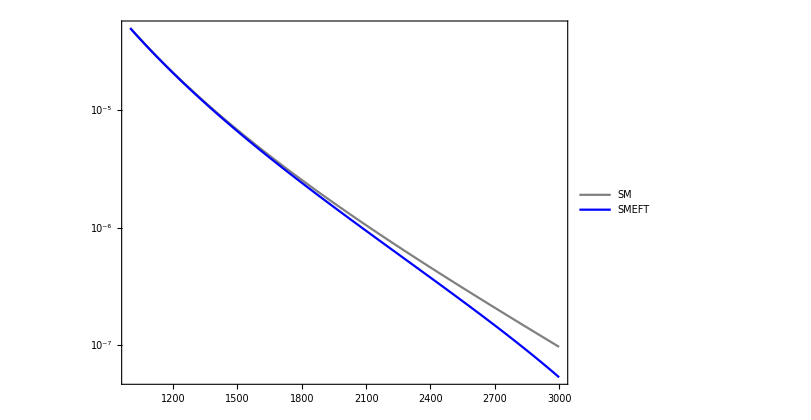

/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/pp2lnu_SMvsSMEFT.pdf

```mathematica
legend=Placed[LineLegend[{"SM","SMEFT"},LegendFunction->(Framed[#,Background->White]&),LegendMargins->5,LegendLayout->"Column"],{0.9,0.9}];
plot1=LogPlot[{dσdMudbarSMinterpol[M],dσdMudbarSMEFTinterpol[M]},{M,1000,3000},PlotStyle->{Gray,Blue},PlotLegends->legend]
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha_scheme_pp2lnu_SMvsSMEFT.pdf",plot1]
```

## 4. Dilepton Final State (Not fully evaluated)

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

### Definitions

```mathematica
SetOptions[{Plot,LogPlot,LogLogPlot,ListPlot,ListLogLogPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,PlotStyle->{Thick},GridLines->Full];
SetOptions[{ListContourPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,ContourLabels->True]; (*Plot with frames*)

Clear[Q,L,mz,e,θw,Mll];
$Assumptions=InM>0&&mz>0&&M>0;
FCClearScalarProducts[];

Definitions;

Sw=Sin[θw];Cw=Cos[θw];
(*g = e/Sw*)
PL=ChiralityProjector[-1];PR=ChiralityProjector[+1];

(*Chirality dependent*)
(* uLA, dLA, uLZ, dLZ, uRA, dRA, uRZ, dRZ, eLA, eLZ, eRA, eRZ *)
gL[x_]:=Switch[x,ν,νLZ,l,eLZ,u,uLZ,d,dLZ];
gR[x_]:=Switch[x,ν,νRZ,l,eRZ,u,uRZ,d,dRZ];
(* W depedning on *)
                                                         (* W^+ν̄ γ Subscript[P, L] e         W^-ē γ Subscript[P, L] ν             W^+ū γ Subscript[P, L] d             W^-ū γ Subscript[P, R] d            W^+d̄ γ Subscript[P, L] u           W^-d̄ γ Subscript[P, R] u *)
gwcoupling[x_]:=Switch[x,νbareL,νbareLWp*PL,ebarνL,ebarνLWm*PL,ubardL,ubardLWp*PL,ubardR,ubardRWp*PR,dbaruL,dbaruLWm*PL,dbaruR,dbaruRWm*PR];

Q[x_]:=Switch[x,ν,νLA*PL+νRA*PR,l,eLA*PL+eRA*PR,u,uLA*PL+uRA*PR,d,dLA*PL+dRA*PR];
(*MassReplace[x_]:=x/.{mz->91.1876,Γz->2.4952, α->1/127.91,mh->100};*)


Couplings;

(*Chirality dependent*)
gz[q_,μ_]:=ⅈ GA[μ].((gL[q])+(gR[q]));
gγ[q_,μ_]:=ⅈ Q[q] GA[μ]/.PL->1-PR//Simplify;
gw[q_,μ_]:=ⅈ GA[μ].gwcoupling[q];

Propagators;
lProp[p_,m_]:=(ⅈ(FV[p,α]GA[α]+m))/(SP[p]-m^2)//DiracSimplify;
ScalarProp[p_,m_]:=ⅈ/(SP[p]-m^2);
γProp[p_,x_,y_]:=(-ⅈ MT[x,y]/SP[p]);
zProp[p_,α_,β_,flag_]:=( -ⅈ/(SP[p]-mz^2+ⅈ Γz mz))(MT[α,β]-flag(FV[p,α]FV[p,β])/SP[p])//Normal; (*Flag=0 to exclude second part (EoM reducible)*)
wProp[p_,α_,β_,flag_]:=( -ⅈ/(SP[p]-mw^2+ⅈ Γw mw))(MT[α,β]-flag(FV[p,α]FV[p,β])/SP[p])//Normal;
RelFermDiagramSign=-1;

GeVtoPB = 1/(2.568*10^-9);
```

### Kinematics

```mathematica
SP[p1,p1]=mp1^2; SP[p2,p2]=mp2^2;
SP[p3,p3]=mp3^2; SP[p4,p4]=mp4^2;
SP[p1,p2] = 2 Ein^2; SP[p3,p4]=2 Ein^2-mp1^2;
SP[p1,p3]=Ein^2-Ein^2 Cθ;
SP[p1,p4]=Ein^2+Ein^2 Cθ;
SP[p2,p3]=Ein^2+Ein^2 Cθ ;
SP[p2,p4]=Ein^2-Ein^2 Cθ; (* Better for proton level calculation *)

mp1=0;
mp2=0;
mp3=0;
mp4=0;
```

### Amplitude q̄ q → e^+e^-

#### GeoSMEFT Amplitude

```mathematica
LLStruc= (SpinorVBar[p2,mp2].GA[μ].PL.SpinorU[p1,mp1])MT[μ,ν](SpinorUBar[p3,mp3].GA[ν].PL.SpinorV[p4,mp4])//DiracSimplify;
RLStruc=  (SpinorVBar[p2,mp2].GA[μ].PR.SpinorU[p1,mp1])MT[μ,ν](SpinorUBar[p3,mp3].GA[ν].PL.SpinorV[p4,mp4])//DiracSimplify;
LRStruc= (SpinorVBar[p2,mp2].GA[μ].PL.SpinorU[p1,mp1])MT[μ,ν](SpinorUBar[p3,mp3].GA[ν].PR.SpinorV[p4,mp4])//DiracSimplify;
RRStruc=  (SpinorVBar[p2,mp2].GA[μ].PR.SpinorU[p1,mp1])MT[μ,ν](SpinorUBar[p3,mp3].GA[ν].PR.SpinorV[p4,mp4])//DiracSimplify;

zPropOx=zProp[p1+p2,μ,ν,0]/.MT[μ,ν]->1;
γPropOx=γProp[p1+p2,μ,ν]/.MT[μ,ν]->1;
```

#### Contact Terms

```mathematica
(* Definitions *)
contactterms=ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/contact_terms.txt"]];

CuLeL=Coefficient[contactterms, edag σbarμ e udag σbarμ u];
CuReL=Coefficient[contactterms, edag σbarμ e uc σμ ucdag];
CuLeR=Coefficient[contactterms, ec σμ ecdag udag σbarμ u];
CuReR=Coefficient[contactterms, ec σμ ecdag uc σμ ucdag];
CdLeL=Coefficient[contactterms, edag σbarμ e ddag σbarμ d];
CdReL=Coefficient[contactterms, edag σbarμ e dc σμ dcdag];
CdLeR=Coefficient[contactterms, ec σμ ecdag ddag σbarμ d];
CdReR=Coefficient[contactterms, ec σμ ecdag dc σμ dcdag];
```

```mathematica
Cqe1[cont_]:=SeriesCoefficient[cont,{x,0,1}] x
Cqe2[cont_]:=Coefficient[SeriesCoefficient[cont,{x,0,2}] ,vT^-2] x^2 vT^-2
Cqes[cont_]:=Coefficient[SeriesCoefficient[cont,{x,0,2}] ,s] x^2
Cqet[cont_]:=Coefficient[SeriesCoefficient[cont,{x,0,2}] ,t] x^2
```

#### Decay Width of Z

```mathematica
Zdecaywidth=Series[ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/mW_scheme-Z_decay_width.txt"]],{x,0,2}];
Γz0val=SeriesCoefficient[Zdecaywidth//Expand,{x,0,0}];
Γz1val=SeriesCoefficient[Zdecaywidth//Expand,{x,0,1}];
Γz2val=SeriesCoefficient[Zdecaywidth//Expand,{x,0,2}]//Expand;
```

#### Amplitude Square GeoSMEFT

```mathematica
LLchiralSq=FermionSpinSum[Normal[Series[LLStruc*ComplexConjugate[(LLStruc)/.{ μ->ρ}],{x,0,2}]]]/.DiracTrace->Tr //Contract //Simplify;
RLchiralSq=FermionSpinSum[Normal[Series[RLStruc*ComplexConjugate[(RLStruc)/.{ μ->ρ}],{x,0,2}]]]/.DiracTrace->Tr //Contract //Simplify;
LRchiralSq=FermionSpinSum[Normal[Series[LRStruc*ComplexConjugate[(LRStruc)/.{ μ->ρ}],{x,0,2}]]]/.DiracTrace->Tr //Contract //Simplify;
RRchiralSq=FermionSpinSum[Normal[Series[RRStruc*ComplexConjugate[(RRStruc)/.{ μ->ρ}],{x,0,2}]]]/.DiracTrace->Tr //Contract //Simplify;
(* LLchiralSq = RRchiralSq *)
(* RLchiralSq = LRchiralSq *)
```

```mathematica
ampLLnostruc=1/ⅈ(ⅈ qLZ zPropOx ⅈ eLZ+ⅈ qLA γPropOx ⅈ eLA+(ⅈ CqLeL1 x+ⅈ CqLeL2 x^2+ⅈ CqLeLs s x^2+ⅈ CqLeLt t x^2))//.{s->2SP[p1,p2], t->-2SP[p1,p3],SP[p1+p2]->s}//Simplify;

ampLLnostrucSq[order_]:=SeriesCoefficient[ComplexExpand[ampLLnostruc*ComplexExpand[Conjugate[ampLLnostruc(*/.qLZ->qLZstar/.eLZ->eLZstar*)]]]/.Γz->Γz0+Γz1 x+Γz2 x^2,{x,0,order}]//Normal
```

```mathematica
str1=Coefficient[ampLLnostrucSq[0],eLZ^2 qLZ^2]//Simplify;
str2=Coefficient[ampLLnostrucSq[0],eLA^2 qLA^2]//Simplify;
str3=Coefficient[ampLLnostrucSq[0],eLA qLA eLZ qLZ]//Simplify;

str4=Coefficient[ampLLnostrucSq[1],CqLeL1 eLA qLA]//Simplify;
str5=Coefficient[ampLLnostrucSq[1],CqLeL1 eLZ qLZ]//Simplify;
str6=Coefficient[ampLLnostrucSq[1],Γz1 eLA qLA eLZ qLZ]//Simplify;
str7=Coefficient[ampLLnostrucSq[1],Γz1 eLZ^2 qLZ^2]//Simplify;

str8=Coefficient[ampLLnostrucSq[2],CqLeL1^2]//Simplify;
str9=Coefficient[ampLLnostrucSq[2],CqLeL1 Γz1 eLZ qLZ]//Simplify;
str10=Coefficient[ampLLnostrucSq[2], Γz1^2 eLA qLA eLZ qLZ]//Simplify;
str11=Coefficient[ampLLnostrucSq[2], Γz1^2 eLZ^2 qLZ^2]//Simplify;
str12=Coefficient[ampLLnostrucSq[2], Γz2 eLA qLA eLZ qLZ]//Simplify;
str13=Coefficient[ampLLnostrucSq[2], Γz2 eLZ^2 qLZ^2]//Simplify;
str14=Coefficient[ampLLnostrucSq[2],CqLeL2 eLA qLA]//Simplify;
str15=Coefficient[ampLLnostrucSq[2],CqLeL2 eLZ qLZ]//Simplify;
str16=Coefficient[ampLLnostrucSq[2],CqLeLs eLA qLA]//Simplify;
str17=Coefficient[ampLLnostrucSq[2],CqLeLs eLZ qLZ]//Simplify;
str18=Coefficient[ampLLnostrucSq[2],CqLeLt eLA qLA]//Simplify;
str19=Coefficient[ampLLnostrucSq[2],CqLeLt eLZ qLZ]//Simplify;
```

```mathematica
LLstructures={str1,str2,str3,str4,str5,str6,str7,str8,str9,str10,str11,str12,str13,str14,str15,str16,str17,str18,str19};
LLcouplings={eLZ^2 qLZ^2,eLA^2 qLA^2,eLA qLA eLZ qLZ,
CqLeL1 eLA qLA,CqLeL1 eLZ qLZ,Γz1 eLA qLA eLZ qLZ,Γz1 eLZ^2 qLZ^2,
CqLeL1^2,CqLeL1 Γz1 eLZ qLZ,Γz1^2 eLA qLA eLZ qLZ,Γz1^2 eLZ^2 qLZ^2,Γz2 eLA qLA eLZ qLZ,Γz2 eLZ^2 qLZ^2,CqLeL2 eLA qLA,CqLeL2 eLZ qLZ,CqLeLs eLA qLA,CqLeLs eLZ qLZ,CqLeLt eLA qLA,CqLeLt eLZ qLZ};
RLcouplings=LLcouplings/.{qLZ->qRZ,qLA->qRA,CqLeL1->CqReL1,CqLeL2->CqReL2, CqLeLs ->CqReLs,CqLeLt->CqReLt};
LRcouplings=LLcouplings/.{eLZ->eRZ,eLA->eRA,CqLeL1->CqLeR1,CqLeL2->CqLeR2, CqLeLs ->CqLeRs,CqLeLt->CqLeRt};
RRcouplings=LLcouplings/.{qLZ->qRZ,qLA->qRA,eLZ->eRZ,eLA->eRA,CqLeL1->CqReR1,CqLeL2->CqReR2, CqLeLs ->CqReRs,CqLeLt->CqReRt};
```

#### dσ/dΩ Parton level

```mathematica
qq2lldσdΩLL =1/(64 π^2  4 Ein^2)(*Phase Space*)1/3(*Color Av.*)1/4(*Spin Av.*) LLchiralSq LLstructures (* Same as RR *)/.{mz->91.1876,mw->80.387,Γz0->Γz0val};
qq2lldσdΩRL =1/(64 π^2  4 Ein^2)(*Phase Space*)1/3(*Color Av.*)1/4(*Spin Av.*) RLchiralSq LLstructures (* Same as LR *)/.{mz->91.1876,mw->80.387,Γz0->Γz0val};
```

```mathematica
qq2llσLL=2π Integrate[qq2lldσdΩLL,{Cθ,-1,1}]/.Ein->M/2//Simplify
qq2llσRL=2π Integrate[qq2lldσdΩRL,{Cθ,-1,1}]/.Ein->M/2//Simplify
```

{(0.00221049 M^2)/(M^4-16630.4 M^2+6.91919×10^7),1/(144 π M^2),(0.00442097 M^2-36.7612)/(M^4-16630.4 M^2+6.91919×10^7),1/(72 π),(0.00442097 M^2 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7),(1.49426×10^6-179.703 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),-(89.8516 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),M^2/(144 π),-(179.703 M^2 (M^2-8315.18))/((M^4-16630.4 M^2+6.91919×10^7)^2),-(36.7612 (M^2-8315.18) (M^4-16630.4 M^2+6.89932×10^7))/((M^4-16630.4 M^2+6.91919×10^7)^3),(-18.3806 M^6+305676. M^4-1.26813×10^9 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^3),(1.49426×10^6-179.703 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),-(89.8516 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),1/(72 π),(0.00442097 M^2 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7),M^2/(72 π),(0.00442097 M^4 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7),-M^2/(288 π),-(0.00110524 M^4 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7)}

{(0.00221049 M^2)/(M^4-16630.4 M^2+6.91919×10^7),1/(144 π M^2),(0.00442097 M^2-36.7612)/(M^4-16630.4 M^2+6.91919×10^7),1/(72 π),(0.00442097 M^2 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7),(1.49426×10^6-179.703 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),-(89.8516 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),M^2/(144 π),-(179.703 M^2 (M^2-8315.18))/((M^4-16630.4 M^2+6.91919×10^7)^2),-(36.7612 (M^2-8315.18) (M^4-16630.4 M^2+6.89932×10^7))/((M^4-16630.4 M^2+6.91919×10^7)^3),(-18.3806 M^6+305676. M^4-1.26813×10^9 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^3),(1.49426×10^6-179.703 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),-(89.8516 M^2)/((M^4-16630.4 M^2+6.91919×10^7)^2),1/(72 π),(0.00442097 M^2 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7),M^2/(72 π),(0.00442097 M^4 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7),-M^2/(96 π),-(0.00331573 M^4 (M^2-8315.18))/(M^4-16630.4 M^2+6.91919×10^7)}

### PDF Apply based on Helicity Structure

```mathematica
SetDirectory["~/Google\ Drive/Research/Instruction/Tools/Cuba-4.2.1"];
Install["Vegas"];
```

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/math_package_v2";
SetDirectory[pdfpath];
<< NNPDF`
prefix=pdfpath<>"/Grids/";
namegrid = "NNPDF30_nlo_as_0118";
Timing[InitializePDFGrid[prefix,namegrid]]
```

Welcome in the Mathematica Package for NNPDF PDFs. The following Functions are available:

- Initializing and interpolating PDFs

InitializePDFGrid;

- Using NNPDF PDFs

xPDFcv; xPDFEnsemble; xPDFRep; xPDF; xPDFCL; xMin; xMax; Q2min; Q2Max; NumberPDF; HasPhoton;

- Parameters for the QCD analysis

alphaSMZ; mCharm; mBottom; mTop; MZ; alphas; Infoalphas; Lam4; Lam5;

For the usage of each of these Functions, please read the README file or type ?Function.

'Version' '5.8.8'

'Description:'

'NNPDF30_nlo_as_0118.LHgrid'

'Reference: arXiv:1410.8849'

'Fit: NLO global fit, alphas(MZ)=0.118'

'NNPDF Collaboration: R.D. Ball, V. Bertone, '

'S. Carrazza, C.S. Deans, L. Del Debbio, '

'S. Forte, A. Guffanti, N.P. Hartland, '

'J.I. Latorre, J. Rojo and M. Ubiali'

'This set has 100 member PDF'

'mem=0 --> average on replicas.'

'Evolution: pol. interpolation on the LH grid'

Grid division:

x axis: 100 points; 1.×10^-9 <= x <= 1.

Q^2 axis: 50 points; 1. <= Q^2 <= 1.×10^10

Reading PDF set from file. Please wait.

PDF set successfully read from file.

Interpolating PDF set on the grid. Please wait.

PDF grid interpolated. Ready to use the NNPDF set.

{12.5326,Null}

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;


(*pdf[x_,Q_,flav_]:=If[x≤1.0&&x>10^-9&&xPDFcv[x,Q^2,flav]>0,1/x xPDFcv[x,Q^2,flav],0]*)
pdf[x_,flav_]:=xPDFcv[x,mz^2,flav]/.mz->91.1876/.mw->80.387

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0,    3 (strange),  4(charm)  *)

uubarpdf=2/M(pdf[M/(√scoll)Exp[Y],2]pdf[M/(√scoll)Exp[-Y],-2]+pdf[M/(√scoll)Exp[Y],-2]pdf[M/(√scoll)Exp[-Y], 2]);
ddbarpdf=2/M(pdf[M/(√scoll)Exp[Y],1]pdf[M/(√scoll)Exp[-Y],-1]+pdf[M/(√scoll)Exp[Y],-1]pdf[M/(√scoll)Exp[-Y], 1]);
ccbarpdf=2/M(pdf[M/(√scoll)Exp[Y],4]pdf[M/(√scoll)Exp[-Y],-4]+pdf[M/(√scoll)Exp[Y],-4]pdf[M/(√scoll)Exp[-Y], 4]);
ssbarpdf=2/M(pdf[M/(√scoll)Exp[Y],3]pdf[M/(√scoll)Exp[-Y],-3]+pdf[M/(√scoll)Exp[Y],-3]pdf[M/(√scoll)Exp[-Y], 3]);
```

```mathematica
σpp2llOxuubar={};
σpp2llOxddbar={};
σpp2llOxccbar={};
σpp2llOxssbar={};
Monitor[Do[
protonσuu=1/10^5 Vegas[10^5 GeVtoPB qq2llσLL[[i]]uubarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 5000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal -> 3,AccuracyGoal-> 3, Verbose->0];
protonσdd=1/10^5 Vegas[10^5 GeVtoPB qq2llσLL[[i]]ddbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 5000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal -> 3,AccuracyGoal-> 3, Verbose->0];
protonσcc=1/10^5 Vegas[10^5 GeVtoPB qq2llσLL[[i]]ccbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 5000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal -> 3,AccuracyGoal-> 3, Verbose->0];
protonσss=1/10^5 Vegas[10^5 GeVtoPB qq2llσLL[[i]]ssbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 5000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal -> 3,AccuracyGoal-> 3, Verbose->0];
AppendTo[σpp2llOxuubar,{LLcouplings[[i]],protonσuu}];
AppendTo[σpp2llOxddbar,{LLcouplings[[i]],protonσdd}];
AppendTo[σpp2llOxccbar,{LLcouplings[[i]],protonσcc}];
AppendTo[σpp2llOxssbar,{LLcouplings[[i]],protonσss}];
,{i,1,Length[qq2llσLL]}],i];
σpp2llOxuubar
σpp2llOxddbar
σpp2llOxccbar
σpp2llOxssbar
```

Vegas::success: Needed 1000000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 5200000 function evaluations.

General::stop: Further output of Vegas::accuracy will be suppressed during this calculation.

(eLZ^2 qLZ^2 | (114615. | 60.898 | 4.43501×10^-9)
eLA^2 qLA^2 | (2.72243×10^8 | 149456. | 2.35593×10^-6)
eLA eLZ qLA qLZ | (-222817. | 163.095 | 3.98918×10^-8)
CqLeL1 eLA qLA | (1.8566×10^9 | 1.02518×10^6 | 4.11822×10^-8)
CqLeL1 eLZ qLZ | (1.09414×10^6 | 72335.3 | 3.33067×10^-21)
Γz1 eLA eLZ qLA qLZ | (230.08 | 0.831207 | 4.86211×10^-17)
Γz1 eLZ^2 qLZ^2 | (-46993.9 | 22.7438 | 1.30649×10^-7)
CqLeL1^2 | (2.27813×10^12 | 1.66798×10^9 | 4.43706×10^-9)
CqLeL1 Γz1 eLZ qLZ | (266373. | 6389.48 | 2.17115×10^-17)
Γz1^2 eLA eLZ qLA qLZ | (26.4872 | 0.211812 | 1.47993×10^-17)
Γz1^2 eLZ^2 qLZ^2 | (19237. | 11.9771 | 1.98986×10^-8)
Γz2 eLA eLZ qLA qLZ | (230.08 | 0.831207 | 4.86211×10^-17)
Γz2 eLZ^2 qLZ^2 | (-46993.9 | 22.7438 | 1.30649×10^-7)
CqLeL2 eLA qLA | (1.8566×10^9 | 1.02518×10^6 | 4.11822×10^-8)
CqLeL2 eLZ qLZ | (1.09414×10^6 | 72335.3 | 3.33067×10^-21)
CqLeLs eLA qLA | (4.55627×10^12 | 3.33596×10^9 | 4.43706×10^-9)
CqLeLs eLZ qLZ | (4.55407×10^12 | 3.92098×10^9 | 3.33585×10^-10)
CqLeLt eLA qLA | (-1.13907×10^12 | 8.3399×10^8 | 4.43706×10^-9)
CqLeLt eLZ qLZ | (-1.13852×10^12 | 9.80244×10^8 | 3.33585×10^-10))

(eLZ^2 qLZ^2 | (83464.1 | 44.7793 | 3.44426×10^-9)
eLA^2 qLA^2 | (2.34089×10^8 | 131891. | 1.061×10^-6)
eLA eLZ qLA qLZ | (-187587. | 132.509 | 1.30696×10^-8)
CqLeL1 eLA qLA | (1.55969×10^9 | 835582. | 1.55496×10^-8)
CqLeL1 eLZ qLZ | (-2.30064×10^6 | 52555.7 | 7.77156×10^-21)
Γz1 eLA eLZ qLA qLZ | (184.236 | 0.609463 | 2.22157×10^-16)
Γz1 eLZ^2 qLZ^2 | (-34190.1 | 16.4159 | 8.47853×10^-8)
CqLeL1^2 | (1.32197×10^12 | 9.87212×10^8 | 4.35104×10^-9)
CqLeL1 Γz1 eLZ qLZ | (208806. | 4611.95 | 3.67228×10^-17)
Γz1^2 eLA eLZ qLA qLZ | (22.3526 | 0.156402 | 9.17733×10^-17)
Γz1^2 eLZ^2 qLZ^2 | (13994.8 | 8.96311 | 8.94587×10^-9)
Γz2 eLA eLZ qLA qLZ | (184.236 | 0.609463 | 2.22157×10^-16)
Γz2 eLZ^2 qLZ^2 | (-34190.1 | 16.4159 | 8.47853×10^-8)
CqLeL2 eLA qLA | (1.55969×10^9 | 835582. | 1.55496×10^-8)
CqLeL2 eLZ qLZ | (-2.30064×10^6 | 52555.7 | 7.77156×10^-21)
CqLeLs eLA qLA | (2.64393×10^12 | 1.97442×10^9 | 4.35104×10^-9)
CqLeLs eLZ qLZ | (2.61655×10^12 | 2.52256×10^9 | 3.72703×10^-10)
CqLeLt eLA qLA | (-6.60983×10^11 | 4.93606×10^8 | 4.35104×10^-9)
CqLeLt eLZ qLZ | (-6.54136×10^11 | 6.30641×10^8 | 3.72703×10^-10))

(eLZ^2 qLZ^2 | (20038.9 | 10.2202 | 1.17795×10^-9)
eLA^2 qLA^2 | (1.28787×10^8 | 73537.2 | 2.60875×10^-7)
eLA eLZ qLA qLZ | (-94999.4 | 60.062 | 1.7896×10^-9)
CqLeL1 eLA qLA | (7.85867×10^8 | 440514. | 1.90137×10^-9)
CqLeL1 eLZ qLZ | (-4.89867×10^6 | 12569.3 | 1.11022×10^-21)
Γz1 eLA eLZ qLA qLZ | (76.2254 | 0.157076 | 1.03222×10^-15)
Γz1 eLZ^2 qLZ^2 | (-8150.36 | 4.0462 | 1.14679×10^-7)
CqLeL1^2 | (1.08608×10^11 | 9.97701×10^7 | 4.98529×10^-10)
CqLeL1 Γz1 eLZ qLZ | (71379.5 | 1113. | 5.12928×10^-15)
Γz1^2 eLA eLZ qLA qLZ | (11.4071 | 0.039821 | 6.85717×10^-14)
Γz1^2 eLZ^2 qLZ^2 | (3336.04 | 2.09445 | 1.18556×10^-8)
Γz2 eLA eLZ qLA qLZ | (76.2254 | 0.157076 | 1.03222×10^-15)
Γz2 eLZ^2 qLZ^2 | (-8150.36 | 4.0462 | 1.14679×10^-7)
CqLeL2 eLA qLA | (7.85867×10^8 | 440514. | 1.90137×10^-9)
CqLeL2 eLZ qLZ | (-4.89867×10^6 | 12569.3 | 1.11022×10^-21)
CqLeLs eLA qLA | (2.17216×10^11 | 1.9954×10^8 | 4.98529×10^-10)
CqLeLs eLZ qLZ | (1.74496×10^11 | 1.66336×10^8 | 6.04475×10^-18)
CqLeLt eLA qLA | (-5.43041×10^10 | 4.9885×10^7 | 4.98529×10^-10)
CqLeLt eLZ qLZ | (-4.3624×10^10 | 4.1584×10^7 | 6.04492×10^-18))

(eLZ^2 qLZ^2 | (31154. | 15.6958 | 5.98948×10^-10)
eLA^2 qLA^2 | (1.65018×10^8 | 91325.1 | 2.94233×10^-7)
eLA eLZ qLA qLZ | (-124210. | 78.327 | 3.36327×10^-9)
CqLeL1 eLA qLA | (1.02777×10^9 | 566226. | 3.55563×10^-9)
CqLeL1 eLZ qLZ | (-6.18783×10^6 | 19327.8 | 2.33147×10^-20)
Γz1 eLA eLZ qLA qLZ | (103.855 | 0.238672 | 3.05326×10^-15)
Γz1 eLZ^2 qLZ^2 | (-12695.2 | 6.42895 | 4.43847×10^-8)
CqLeL1^2 | (2.07915×10^11 | 1.71281×10^8 | 5.54165×10^-9)
CqLeL1 Γz1 eLZ qLZ | (104128. | 1725.09 | 7.04195×10^-15)
Γz1^2 eLA eLZ qLA qLZ | (14.899 | 0.0602058 | 1.61956×10^-14)
Γz1^2 eLZ^2 qLZ^2 | (5195.86 | 3.37284 | 2.14587×10^-8)
Γz2 eLA eLZ qLA qLZ | (103.855 | 0.238672 | 3.05326×10^-15)
Γz2 eLZ^2 qLZ^2 | (-12695.2 | 6.42895 | 4.43847×10^-8)
CqLeL2 eLA qLA | (1.02777×10^9 | 566226. | 3.55563×10^-9)
CqLeL2 eLZ qLZ | (-6.18783×10^6 | 19327.8 | 2.33147×10^-20)
CqLeLs eLA qLA | (4.15831×10^11 | 3.42562×10^8 | 5.54165×10^-9)
CqLeLs eLZ qLZ | (3.61309×10^11 | 3.58137×10^8 | 5.37414×10^-14)
CqLeLt eLA qLA | (-1.03958×10^11 | 8.56404×10^7 | 5.54165×10^-9)
CqLeLt eLZ qLZ | (-9.03274×10^10 | 8.95342×10^7 | 5.37414×10^-14))

```mathematica
uu2llOx0=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxuubar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxuubar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxuubar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxuubar[[i,2,1,1]],{i,1,19}]//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,0}]
uu2llOx1=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxuubar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxuubar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxuubar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxuubar[[i,2,1,1]],{i,1,19}]//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,1}]//Expand
uu2llOx2=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxuubar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxuubar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxuubar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxuubar[[i,2,1,1]],{i,1,19}]//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,2}]//Expand
```

4.37039×10^6

-1939.2 CeQ6til-1940.31 Ceu6til-1.52394×10^7 CHD6til+115.495 CHdc16til-1789.21 CHec16til+721.937 CHL16til+203.691 CHL36til-1620.82 CHQ16til+297.075 CHQ36til+704.45 CHuc16til-3.26416×10^7 CHWB6til+1940.94 CLQ36til-1940.94 CLQ6til-1939.57 CLu6til-1.23604×10^7 δGF6

619.852 CeQ6til^2+3381.3 CeQ6til CHD6til-0.0837545 CeQ6til CHdc16til-1.82363 CeQ6til CHec16til-0.0837545 CeQ6til CHL16til+0.292064 CeQ6til CHL36til-0.887521 CeQ6til CHQ16til+1.84747 CeQ6til CHQ36til+0.111673 CeQ6til CHuc16til+7244.78 CeQ6til CHWB6til+5484.25 CeQ6til δGF6+12.6443 CeQs8til-9.4832 CeQt8til+619.852 Ceu6til^2+3383.82 Ceu6til CHD6til+0.0354087 Ceu6til CHdc16til+0.770974 Ceu6til CHec16til+0.0354087 Ceu6til CHL16til-0.123476 Ceu6til CHL36til-0.091245 Ceu6til CHQ16til-0.31459 Ceu6til CHQ36til-1.15056 Ceu6til CHuc16til+7246.54 Ceu6til CHWB6til+5488.3 Ceu6til δGF6+50.5203 Ceus8til-12.6301 Ceut8til-3.26416×10^7 CHB6til CHWB6til-1.30544×10^7 CHD28til+1.32863×10^7 CHD6til^2-236.626 CHD6til CHdc16til+1701.33 CHD6til CHec16til+1184.38 CHD6til CHL16til+1342.56 CHD6til CHL36til+2476.42 CHD6til CHQ16til-2475.14 CHD6til CHQ36til+1337.5 CHD6til CHuc16til+7.72133×10^7 CHD6til CHWB6til-3380.96 CHD6til CLQ36til+3380.96 CHD6til CLQ6til+3382.14 CHD6til CLu6til+4.31038×10^7 CHD6til δGF6-2.18503×10^6 CHD8til-367.701 CHdc16til^2-161.978 CHdc16til CHec16til+294.777 CHdc16til CHL16til+106.472 CHdc16til CHL36til-386.952 CHdc16til CHQ16til-94.0303 CHdc16til CHQ36til+62.0559 CHdc16til CHuc16til-191.607 CHdc16til CHWB6til-0.104155 CHdc16til CLQ36til+0.104155 CHdc16til CLQ6til-0.0440334 CHdc16til CLu6til-163.019 CHdc16til δGF6+57.7477 CHdc18til+943.051 CHec16til^2+90.8335 CHec16til CHL16til+817.652 CHec16til CHL36til+4776.53 CHec16til CHQ16til-2920.03 CHec16til CHQ36til+1127.65 CHec16til CHuc16til+2333.07 CHec16til CHWB6til-0.104155 CHec16til CLQ36til+0.104155 CHec16til CLQ6til-0.0440334 CHec16til CLu6til+3635.21 CHec16til δGF6-894.605 CHec18til-969.602 CHeQ18til+969.602 CHeQ38til-970.154 CHeu8til+1270.24 CHL16til^2+1736.03 CHL16til CHL36til-2462.55 CHL16til CHQ16til-916.016 CHL16til CHQ36til+3081.49 CHL16til CHuc16til+3121.25 CHL16til CHWB6til+1.63572 CHL16til CLQ36til-1.63572 CHL16til CLQ6til+0.691532 CHL16til CLu6til+91.5715 CHL16til δGF6+360.968 CHL18til+101.846 CHL28til+370.012 CHL36til^2-726.24 CHL36til CHQ16til-494.088 CHL36til CHQ36til+2803.03 CHL36til CHuc16til+3013.25 CHL36til CHWB6til+2.10308 CHL36til CLQ36til-2.10308 CHL36til CLQ6til+0.889117 CHL36til CLu6til+823.064 CHL36til δGF6+101.846 CHL38til-970.472 CHLQ18til+970.472 CHLQ28til-970.472 CHLQ38til+970.472 CHLQ48til-969.786 CHLu18til-969.786 CHLu38til+1300.82 CHQ16til^2+278.653 CHQ16til CHQ36til+211.836 CHQ16til CHuc16til+1393.39 CHQ16til CHWB6til-1.1037 CHQ16til CLQ36til+1.1037 CHQ16til CLQ6til+0.11347 CHQ16til CLu6til+1990.2 CHQ16til δGF6-810.41 CHQ18til+148.537 CHQ28til-377.833 CHQ36til^2-923.087 CHQ36til CHuc16til-2100.59 CHQ36til CHWB6til+2.29747 CHQ36til CLQ36til-2.29747 CHQ36til CLQ6til+0.391217 CHQ36til CLu6til-121.765 CHQ36til δGF6+148.537 CHQ38til+711.655 CHuc16til^2+1416.23 CHuc16til CHWB6til+0.138873 CHuc16til CLQ36til-0.138873 CHuc16til CLQ6til+1.43081 CHuc16til CLu6til-1291.18 CHuc16til δGF6+352.225 CHuc18til-2.17388×10^7 CHW28til-3.26416×10^7 CHW6til CHWB6til+9.14335×10^7 CHWB6til^2-7242.93 CHWB6til CLQ36til+7242.93 CHWB6til CLQ6til+7245.37 CHWB6til CLu6til+9.23249×10^7 CHWB6til δGF6-4.94717×10^11 CHWB8til+619.852 CLQ36til^2-1239.7 CLQ36til CLQ6til-5490.63 CLQ36til δGF6+619.852 CLQ6til^2+5490.63 CLQ6til δGF6+72.3713 CLQs18til-72.3713 CLQs38til-18.0928 CLQt18til+18.0928 CLQt38til+619.852 CLu6til^2+5485.6 CLu6til δGF6+25.2696 CLus8til-18.9522 CLut8til+2.62198×10^7 δGF6^2-1.23604×10^7 δGF8

```mathematica
dd2llOx0=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxddbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxddbar[[i,2,1,1]],{i,1,19}]//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,0}]
dd2llOx1=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxddbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxddbar[[i,2,1,1]],{i,1,19}]//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,1}]//Expand
dd2llOx2=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxddbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxddbar[[i,2,1,1]],{i,1,19}]//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,2}]//Expand
```

939886.

814.521 Ced6til+816.841 CeQ6til-3.27653×10^6 CHD6til-216.706 CHdc16til-1510.57 CHec16til+835.299 CHL16til+351.566 CHL36til+986.385 CHQ16til+306.395 CHQ36til-143.739 CHuc16til-7.01709×10^6 CHWB6til+815.295 CLd6til+812.41 CLQ36til+812.41 CLQ6til-2.65756×10^6 δGF6

359.691 Ced6til^2-1419.41 Ced6til CHD6til+2.30613 Ced6til CHdc16til+0.759458 Ced6til CHec16til-0.0138782 Ced6til CHL16til+0.0483953 Ced6til CHL36til+0.0357628 Ced6til CHQ16til+0.123301 Ced6til CHQ36til+0.0185043 Ced6til CHuc16til-3042.03 Ced6til CHWB6til-2303.92 Ced6til δGF6-14.6258 Ceds8til+3.65645 Cedt8til+359.691 CeQ6til^2-1424.58 CeQ6til CHD6til+0.0795321 CeQ6til CHdc16til-4.35224 CeQ6til CHec16til+0.0795321 CeQ6til CHL16til-0.27734 CeQ6til CHL36til+2.11506 CeQ6til CHQ16til+1.6134 CeQ6til CHQ36til-0.106043 CeQ6til CHuc16til-3046.59 CeQ6til CHWB6til-2309.76 CeQ6til δGF6+7.1359 CeQs8til-5.35192 CeQt8til-7.01709×10^6 CHB6til CHWB6til-2.80674×10^6 CHD28til+2.85829×10^6 CHD6til^2-762.297 CHD6til CHdc16til+2900.35 CHD6til CHec16til+1867.22 CHD6til CHL16til+2127.5 CHD6til CHL36til-1248.4 CHD6til CHQ16til-1383.77 CHD6til CHQ36til+327.96 CHD6til CHuc16til+1.66037×10^7 CHD6til CHWB6til-1421.13 CHD6til CLd6til-1423.78 CHD6til CLQ36til-1423.78 CHD6til CLQ6til+9.26734×10^6 CHD6til δGF6-469795. CHD8til+408.198 CHdc16til^2-593.043 CHdc16til CHec16til-1099.89 CHdc16til CHL16til-1082.98 CHdc16til CHL36til+255.482 CHdc16til CHQ16til+279.25 CHdc16til CHQ36til+5.02424 CHdc16til CHuc16til-767.018 CHdc16til CHWB6til-2.86785 CHdc16til CLd6til-0.0989042 CHdc16til CLQ36til-0.0989042 CHdc16til CLQ6til+431.119 CHdc16til δGF6-108.353 CHdc18til+881.325 CHec16til^2+84.9463 CHec16til CHL16til+762.934 CHec16til CHL36til-2563.33 CHec16til CHQ16til-1610.27 CHec16til CHQ36til+201.46 CHec16til CHuc16til+3368.4 CHec16til CHWB6til+0.0172586 CHec16til CLd6til-0.0989042 CHec16til CLQ36til-0.0989042 CHec16til CLQ6til+2942.78 CHec16til δGF6-755.286 CHec18til+407.261 CHed8til+408.421 CHeQ18til+408.421 CHeQ38til+1186.69 CHL16til^2+1622.23 CHL16til CHL36til+1685.75 CHL16til CHQ16til-50.1482 CHL16til CHQ36til-366.94 CHL16til CHuc16til+3516.59 CHL16til CHWB6til+0.790595 CHL16til CLd6til-4.53068 CHL16til CLQ36til-4.53068 CHL16til CLQ6til-370.685 CHL16til δGF6+417.65 CHL18til+175.783 CHL28til+346.077 CHL36til^2+1035.78 CHL36til CHQ16til+408.351 CHL36til CHQ36til-132.629 CHL36til CHuc16til+3536.42 CHL36til CHWB6til+0.713153 CHL36til CLd6til-4.08688 CHL36til CLQ36til-4.08688 CHL36til CLQ6til+312.333 CHL36til δGF6+175.783 CHL38til+407.647 CHLd18til+407.647 CHLd38til+406.205 CHLQ18til+406.205 CHLQ28til+406.205 CHLQ38til+406.205 CHLQ48til-313.618 CHQ16til^2-573.432 CHQ16til CHQ36til-193.134 CHQ16til CHuc16til-644.338 CHQ16til CHWB6til-0.0444738 CHQ16til CLd6til-2.63024 CHQ16til CLQ36til-2.63024 CHQ16til CLQ6til-1268.39 CHQ16til δGF6+493.192 CHQ18til+153.197 CHQ28til-448.191 CHQ36til^2+136.241 CHQ36til CHuc16til-1153.29 CHQ36til CHWB6til-0.153335 CHQ36til CLd6til-2.00639 CHQ36til CLQ36til-2.00639 CHQ36til CLQ6til-308.268 CHQ36til δGF6+153.197 CHQ38til-207.055 CHuc16til^2+274.311 CHuc16til CHWB6til-0.0230114 CHuc16til CLd6til+0.131872 CHuc16til CLQ36til+0.131872 CHuc16til CLQ6til+202.955 CHuc16til δGF6-71.8695 CHuc18til-4.67389×10^6 CHW28til-7.01709×10^6 CHW6til CHWB6til+1.96582×10^7 CHWB6til^2-3043.55 CHWB6til CLd6til-3047.59 CHWB6til CLQ36til-3047.59 CHWB6til CLQ6til+1.98477×10^7 CHWB6til δGF6-1.06351×10^11 CHWB8til+359.691 CLd6til^2-2305.87 CLd6til δGF6-7.37191 CLds8til+5.52893 CLdt8til+359.691 CLQ36til^2+719.382 CLQ36til CLQ6til-2298.61 CLQ36til δGF6+359.691 CLQ6til^2-2298.61 CLQ6til δGF6-34.4342 CLQs18til-34.4342 CLQs38til+8.60856 CLQt18til+8.60856 CLQt38til+5.63694×10^6 δGF6^2-2.65756×10^6 δGF8

```mathematica
cc2llOx0=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxccbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxccbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxccbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxccbar[[i,2,1,1]],{i,1,19}]//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,0}]
cc2llOx1=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxccbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxccbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxccbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxccbar[[i,2,1,1]],{i,1,19}]//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,1}]//Expand
cc2llOx2=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxccbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxccbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxccbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxccbar[[i,2,1,1]],{i,1,19}]//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,2}]//Expand
```

2.06727×10^6

-824.632 CeQ6til-819.693 Ceu6til-7.20914×10^6 CHD6til+20.0247 CHdc16til-510.541 CHec16til-71.5023 CHL16til-161.356 CHL36til-230.08 CHQ16til+0.568284 CHQ36til+176.252 CHuc16til-1.54415×10^7 CHWB6til+816.843 CLQ36til-816.843 CLQ6til-822.986 CLu6til-5.84697×10^6 δGF6

29.551 CeQ6til^2+1436.98 CeQ6til CHD6til-0.0224435 CeQ6til CHdc16til+7.76734 CeQ6til CHec16til-0.0224435 CeQ6til CHL16til+0.0782639 CeQ6til CHL36til+4.99774 CeQ6til CHQ16til-4.7405 CeQ6til CHQ36til+0.0299247 CeQ6til CHuc16til+3070.66 CeQ6til CHWB6til+2332.24 CeQ6til δGF6+0.85192 CeQs8til-0.63894 CeQt8til+29.551 Ceu6til^2+1425.91 Ceu6til CHD6til+0.0094884 Ceu6til CHdc16til-3.28378 Ceu6til CHec16til+0.0094884 Ceu6til CHL16til-0.0330875 Ceu6til CHL36til-0.0244507 Ceu6til CHQ16til-0.0843001 Ceu6til CHQ36til+4.92725 Ceu6til CHuc16til+3061.35 Ceu6til CHWB6til+2318.51 Ceu6til δGF6+2.3032 Ceus8til-0.575799 Ceut8til-1.54415×10^7 CHB6til CHWB6til-6.17553×10^6 CHD28til+6.28469×10^6 CHD6til^2-41.1153 CHD6til CHdc16til+236.473 CHD6til CHec16til+145.838 CHD6til CHL16til+173.661 CHD6til CHL36til+1071.36 CHD6til CHQ16til-1070.12 CHD6til CHQ36til+871.673 CHD6til CHuc16til+3.65254×10^7 CHD6til CHWB6til-1438.84 CHD6til CLQ36til+1438.84 CHD6til CLQ6til+1433.29 CHD6til CLu6til+2.03905×10^7 CHD6til δGF6-1.03361×10^6 CHD8til-63.7511 CHdc16til^2-28.1489 CHdc16til CHec16til+51.0679 CHdc16til CHL16til+18.4079 CHdc16til CHL36til-67.0964 CHdc16til CHQ16til-16.3265 CHdc16til CHQ36til+10.7773 CHdc16til CHuc16til-33.309 CHdc16til CHWB6til-0.0279102 CHdc16til CLQ36til+0.0279102 CHdc16til CLQ6til-0.0117995 CHdc16til CLu6til-28.2442 CHdc16til δGF6+10.0123 CHdc18til+165.268 CHec16til^2+15.6404 CHec16til CHL16til+141.949 CHec16til CHL36til+1322.01 CHec16til CHQ16til-999.384 CHec16til CHQ36til+683.711 CHec16til CHuc16til+604.955 CHec16til CHWB6til-0.0279102 CHec16til CLQ36til+0.0279102 CHec16til CLQ6til-0.0117995 CHec16til CLu6til+1196.38 CHec16til δGF6-255.271 CHec18til-412.316 CHeQ18til+412.316 CHeQ38til-409.846 CHeu8til+222.021 CHL16til^2+304.747 CHL16til CHL36til+58.0089 CHL16til CHQ16til-643.321 CHL16til CHQ36til+1026.17 CHL16til CHuc16til+744.374 CHL16til CHWB6til-7.81769 CHL16til CLQ36til+7.81769 CHL16til CLQ6til-3.30507 CHL16til CLu6til+571.833 CHL16til δGF6-35.7512 CHL18til-80.6781 CHL28til+66.1471 CHL36til^2+359.081 CHL36til CHQ16til-570.062 CHL36til CHQ36til+977.808 CHL36til CHuc16til+726.045 CHL36til CHWB6til-7.69245 CHL36til CLQ36til+7.69245 CHL36til CLQ6til-3.25212 CHL36til CLu6til+698.569 CHL36til δGF6-80.6781 CHL38til-408.421 CHLQ18til+408.421 CHLQ28til-408.421 CHLQ38til+408.421 CHLQ48til-411.493 CHLu18til-411.493 CHLu38til+227.133 CHQ16til^2+45.1955 CHQ16til CHQ36til+36.6814 CHQ16til CHuc16til+855.944 CHQ16til CHWB6til+6.21507 CHQ16til CLQ36til-6.21507 CHQ16til CLQ6til+0.0304063 CHQ16til CLu6til+200.937 CHQ16til δGF6-115.04 CHQ18til+0.284142 CHQ28til-63.816 CHQ36til^2-160.205 CHQ36til CHuc16til-977.551 CHQ36til CHWB6til-5.89517 CHQ36til CLQ36til+5.89517 CHQ36til CLQ6til+0.104834 CHQ36til CLu6til+122.783 CHQ36til δGF6+0.284142 CHQ38til+124.949 CHuc16til^2+860.876 CHuc16til CHWB6til+0.0372136 CHuc16til CLQ36til-0.0372136 CHuc16til CLQ6til-6.12741 CHuc16til CLu6til-376.782 CHuc16til δGF6+88.126 CHuc18til-1.02838×10^7 CHW28til-1.54415×10^7 CHW6til CHWB6til+4.32529×10^7 CHWB6til^2-3076.68 CHWB6til CLQ36til+3076.68 CHWB6til CLQ6til+3067.55 CHWB6til CLu6til+4.36753×10^7 CHWB6til δGF6-2.34032×10^11 CHWB8til+29.551 CLQ36til^2-59.1019 CLQ36til CLQ6til-2310.6 CLQ36til δGF6+29.551 CLQ6til^2+2310.6 CLQ6til δGF6+3.14045 CLQs18til-3.14045 CLQs38til-0.785113 CLQt18til+0.785113 CLQt38til+29.551 CLu6til^2+2327.66 CLu6til δGF6+1.33568 CLus8til-1.00176 CLut8til+1.24032×10^7 δGF6^2-5.84697×10^6 δGF8

```mathematica
ss2llOx0=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxssbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxssbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxssbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxssbar[[i,2,1,1]],{i,1,19}]//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,0}]
ss2llOx1=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxddbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxddbar[[i,2,1,1]],{i,1,19}]//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,1}]//Expand
ss2llOx2=SeriesCoefficient[ZinvolveCoupling[Sum[LLcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+RRcouplings[[i]]σpp2llOxddbar[[i,2,1,1]]+(RLcouplings[[i]]/.CqReLt->3CqReLt)σpp2llOxddbar[[i,2,1,1]]+(LRcouplings[[i]]/.CqLeRt->3CqLeRt)σpp2llOxddbar[[i,2,1,1]],{i,1,19}]//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,2}]//Expand
```

662367.

814.521 Ced6til+816.841 CeQ6til-3.27653×10^6 CHD6til-216.706 CHdc16til-1510.57 CHec16til+835.299 CHL16til+351.566 CHL36til+986.385 CHQ16til+306.395 CHQ36til-143.739 CHuc16til-7.01709×10^6 CHWB6til+815.295 CLd6til+812.41 CLQ36til+812.41 CLQ6til-2.65756×10^6 δGF6

359.691 Ced6til^2-1419.41 Ced6til CHD6til+2.30613 Ced6til CHdc16til+0.759458 Ced6til CHec16til-0.0138782 Ced6til CHL16til+0.0483953 Ced6til CHL36til+0.0357628 Ced6til CHQ16til+0.123301 Ced6til CHQ36til+0.0185043 Ced6til CHuc16til-3042.03 Ced6til CHWB6til-2303.92 Ced6til δGF6-14.6258 Ceds8til+3.65645 Cedt8til+359.691 CeQ6til^2-1424.58 CeQ6til CHD6til+0.0795321 CeQ6til CHdc16til-4.35224 CeQ6til CHec16til+0.0795321 CeQ6til CHL16til-0.27734 CeQ6til CHL36til+2.11506 CeQ6til CHQ16til+1.6134 CeQ6til CHQ36til-0.106043 CeQ6til CHuc16til-3046.59 CeQ6til CHWB6til-2309.76 CeQ6til δGF6+7.1359 CeQs8til-5.35192 CeQt8til-7.01709×10^6 CHB6til CHWB6til-2.80674×10^6 CHD28til+2.85829×10^6 CHD6til^2-762.297 CHD6til CHdc16til+2900.35 CHD6til CHec16til+1867.22 CHD6til CHL16til+2127.5 CHD6til CHL36til-1248.4 CHD6til CHQ16til-1383.77 CHD6til CHQ36til+327.96 CHD6til CHuc16til+1.66037×10^7 CHD6til CHWB6til-1421.13 CHD6til CLd6til-1423.78 CHD6til CLQ36til-1423.78 CHD6til CLQ6til+9.26734×10^6 CHD6til δGF6-469795. CHD8til+408.198 CHdc16til^2-593.043 CHdc16til CHec16til-1099.89 CHdc16til CHL16til-1082.98 CHdc16til CHL36til+255.482 CHdc16til CHQ16til+279.25 CHdc16til CHQ36til+5.02424 CHdc16til CHuc16til-767.018 CHdc16til CHWB6til-2.86785 CHdc16til CLd6til-0.0989042 CHdc16til CLQ36til-0.0989042 CHdc16til CLQ6til+431.119 CHdc16til δGF6-108.353 CHdc18til+881.325 CHec16til^2+84.9463 CHec16til CHL16til+762.934 CHec16til CHL36til-2563.33 CHec16til CHQ16til-1610.27 CHec16til CHQ36til+201.46 CHec16til CHuc16til+3368.4 CHec16til CHWB6til+0.0172586 CHec16til CLd6til-0.0989042 CHec16til CLQ36til-0.0989042 CHec16til CLQ6til+2942.78 CHec16til δGF6-755.286 CHec18til+407.261 CHed8til+408.421 CHeQ18til+408.421 CHeQ38til+1186.69 CHL16til^2+1622.23 CHL16til CHL36til+1685.75 CHL16til CHQ16til-50.1482 CHL16til CHQ36til-366.94 CHL16til CHuc16til+3516.59 CHL16til CHWB6til+0.790595 CHL16til CLd6til-4.53068 CHL16til CLQ36til-4.53068 CHL16til CLQ6til-370.685 CHL16til δGF6+417.65 CHL18til+175.783 CHL28til+346.077 CHL36til^2+1035.78 CHL36til CHQ16til+408.351 CHL36til CHQ36til-132.629 CHL36til CHuc16til+3536.42 CHL36til CHWB6til+0.713153 CHL36til CLd6til-4.08688 CHL36til CLQ36til-4.08688 CHL36til CLQ6til+312.333 CHL36til δGF6+175.783 CHL38til+407.647 CHLd18til+407.647 CHLd38til+406.205 CHLQ18til+406.205 CHLQ28til+406.205 CHLQ38til+406.205 CHLQ48til-313.618 CHQ16til^2-573.432 CHQ16til CHQ36til-193.134 CHQ16til CHuc16til-644.338 CHQ16til CHWB6til-0.0444738 CHQ16til CLd6til-2.63024 CHQ16til CLQ36til-2.63024 CHQ16til CLQ6til-1268.39 CHQ16til δGF6+493.192 CHQ18til+153.197 CHQ28til-448.191 CHQ36til^2+136.241 CHQ36til CHuc16til-1153.29 CHQ36til CHWB6til-0.153335 CHQ36til CLd6til-2.00639 CHQ36til CLQ36til-2.00639 CHQ36til CLQ6til-308.268 CHQ36til δGF6+153.197 CHQ38til-207.055 CHuc16til^2+274.311 CHuc16til CHWB6til-0.0230114 CHuc16til CLd6til+0.131872 CHuc16til CLQ36til+0.131872 CHuc16til CLQ6til+202.955 CHuc16til δGF6-71.8695 CHuc18til-4.67389×10^6 CHW28til-7.01709×10^6 CHW6til CHWB6til+1.96582×10^7 CHWB6til^2-3043.55 CHWB6til CLd6til-3047.59 CHWB6til CLQ36til-3047.59 CHWB6til CLQ6til+1.98477×10^7 CHWB6til δGF6-1.06351×10^11 CHWB8til+359.691 CLd6til^2-2305.87 CLd6til δGF6-7.37191 CLds8til+5.52893 CLdt8til+359.691 CLQ36til^2+719.382 CLQ36til CLQ6til-2298.61 CLQ36til δGF6+359.691 CLQ6til^2-2298.61 CLQ6til δGF6-34.4342 CLQs18til-34.4342 CLQs38til+8.60856 CLQt18til+8.60856 CLQt38til+5.63694×10^6 δGF6^2-2.65756×10^6 δGF8

```mathematica
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_uu2llSM_M1to13000.txt",uu2llOx0];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_uu2llOx_M1to13000.txt",uu2llOx1];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_uu2llOx2_M1to13000.txt",uu2llOx2];

Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_dd2llSM_M1to13000.txt",dd2llOx0];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_dd2llOx_M1to13000.txt",dd2llOx1];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_dd2llOx2_M1to13000.txt",dd2llOx2];

Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_cc2llSM_M1to13000.txt",cc2llOx0];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_cc2llOx_M1to13000.txt",cc2llOx1];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_cc2llOx2_M1to13000.txt",cc2llOx2];

Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_ss2llSM_M1to13000.txt",ss2llOx0];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_ss2llOx_M1to13000.txt",ss2llOx1];
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha-scheme_ss2llOx2_M1to13000.txt",ss2llOx2];
```

#### σ_SMEFT/σ_SM

```mathematica
σSMdilep=uu2llOx0+dd2llOx0+cc2llOx0+ss2llOx0;
σOxdilep=uu2llOx1+dd2llOx1+cc2llOx1+ss2llOx1;
σOx2dilep=uu2llOx2+dd2llOx2+cc2llOx2+ss2llOx2;
σSMEFTOx=σOxdilep/σSMdilep//Expand
σSMEFTOx2=σOx2dilep/σSMdilep//Expand
```

0.00020262 Ced6til-0.000140568 CeQ6til-0.000343288 Ceu6til-3.60721 CHD6til-0.0000370517 CHdc16til-0.000661811 CHec16til+0.000288689 CHL16til+0.0000927207 CHL36til+0.000015158 CHQ16til+0.000113239 CHQ36til+0.000073785 CHuc16til-7.72612 CHWB6til+0.000202812 CLd6til+0.000545106 CLQ36til-0.000140918 CLQ6til-0.000343606 CLu6til-2.92572 δGF6

0.0000894763 Ced6til^2-0.000353091 Ced6til CHD6til+5.73671×10^-7 Ced6til CHdc16til+1.88922×10^-7 Ced6til CHec16til-3.45233×10^-9 Ced6til CHL16til+1.20388×10^-8 Ced6til CHL36til+8.89633×10^-9 Ced6til CHQ16til+3.06723×10^-8 Ced6til CHQ36til+4.6031×10^-9 Ced6til CHuc16til-0.000756731 Ced6til CHWB6til-0.000573122 Ced6til δGF6-3.6383×10^-6 Ceds8til+9.09575×10^-7 Cedt8til+0.000170249 CeQ6til^2+0.000244918 CeQ6til CHD6til+6.57548×10^-9 CeQ6til CHdc16til-3.43386×10^-7 CeQ6til CHec16til+6.57548×10^-9 CeQ6til CHL16til-2.29297×10^-8 CeQ6til CHL36til+1.03737×10^-6 CeQ6til CHQ16til+4.15138×10^-8 CeQ6til CHQ36til-8.76731×10^-9 CeQ6til CHuc16til+0.000525161 CeQ6til CHWB6til+0.000397638 CeQ6til δGF6+3.45377×10^-6 CeQs8til-2.59033×10^-6 CeQt8til+0.0000807725 Ceu6til^2+0.000598232 Ceu6til CHD6til+5.58428×10^-9 Ceu6til CHdc16til-3.12542×10^-7 Ceu6til CHec16til+5.58428×10^-9 Ceu6til CHL16til-1.94732×10^-8 Ceu6til CHL36til-1.43902×10^-8 Ceu6til CHQ16til-4.96138×10^-8 Ceu6til CHQ36til+4.69743×10^-7 Ceu6til CHuc16til+0.00128209 Ceu6til CHWB6til+0.000971007 Ceu6til δGF6+6.57016×10^-6 Ceus8til-1.64254×10^-6 Ceut8til-7.72612 CHB6til CHWB6til-3.09001 CHD28til+3.14525 CHD6til^2-0.000224174 CHD6til CHdc16til+0.000962512 CHD6til CHec16til+0.000629941 CHD6til CHL16til+0.000717822 CHD6til CHL36til+0.00013072 CHD6til CHQ16til-0.000785182 CHD6til CHQ36til+0.000356359 CHD6til CHuc16til+18.2771 CHD6til CHWB6til-0.00035352 CHD6til CLd6til-0.000953664 CHD6til CLQ36til+0.000245306 CHD6til CLQ6til+0.000598941 CHD6til CLu6til+10.2027 CHD6til δGF6-0.517199 CHD8til+0.0000478791 CHdc16til^2-0.000171173 CHdc16til CHec16til-0.000230591 CHdc16til CHL16til-0.000253869 CHdc16til CHL36til+7.07921×10^-6 CHdc16til CHQ16til+0.00005574 CHdc16til CHQ36til+0.0000103088 CHdc16til CHuc16til-0.000218778 CHdc16til CHWB6til-7.13403×10^-7 CHdc16til CLd6til-4.10295×10^-8 CHdc16til CLQ36til-8.17711×10^-9 CHdc16til CLQ6til-6.94447×10^-9 CHdc16til CLu6til+0.0000834554 CHdc16til δGF6-0.0000185259 CHdc18til+0.00035709 CHec16til^2+0.0000343743 CHec16til CHL16til+0.000309141 CHec16til CHL36til+0.000120883 CHec16til CHQ16til-0.000888065 CHec16til CHQ36til+0.000275411 CHec16til CHuc16til+0.00120335 CHec16til CHWB6til+4.29323×10^-9 CHec16til CLd6til-4.10295×10^-8 CHec16til CLQ36til-8.17711×10^-9 CHec16til CLQ6til-6.94447×10^-9 CHec16til CLu6til+0.00133299 CHec16til δGF6-0.000330905 CHec18til+0.00010131 CHed8til-0.000070284 CHeQ18til+0.000273481 CHeQ38til-0.000171644 CHeu8til+0.000480808 CHL16til^2+0.000657375 CHL16til CHL36til+0.000120269 CHL16til CHQ16til-0.000206424 CHL16til CHQ36til+0.000419628 CHL16til CHuc16til+0.00135559 CHL16til CHWB6til+1.96668×10^-7 CHL16til CLd6til-1.89596×10^-6 CHL16til CLQ36til-3.58138×10^-7 CHL16til CLQ6til-3.2507×10^-7 CHL16til CLu6til-9.69737×10^-6 CHL16til δGF6+0.000144344 CHL18til+0.0000463604 CHL28til+0.000140339 CHL36til^2+0.000211993 CHL36til CHQ16til-0.0000307773 CHL36til CHQ36til+0.000437267 CHL36til CHuc16til+0.00134481 CHL36til CHWB6til+1.77403×10^-7 CHL36til CLd6til-1.71185×10^-6 CHL36til CLQ36til-3.21446×10^-7 CHL36til CLQ6til-2.9391×10^-7 CHL36til CLu6til+0.000266956 CHL36til δGF6+0.0000463604 CHL38til+0.000101406 CHLd18til+0.000101406 CHLd38til-0.000070459 CHLQ18til+0.000272553 CHLQ28til-0.000070459 CHLQ38til+0.000272553 CHLQ48til-0.000171803 CHLu18til-0.000171803 CHLu38til+0.000112031 CHQ16til^2-0.000102366 CHQ16til CHQ36til-0.0000171333 CHQ16til CHuc16til+0.000119486 CHQ16til CHWB6til-1.10633×10^-8 CHQ16til CLd6til-1.85461×10^-8 CHQ16til CLQ36til-1.29004×10^-6 CHQ16til CLQ6til+1.78953×10^-8 CHQ16til CLu6til-0.0000429915 CHQ16til δGF6+7.57898×10^-6 CHQ18til+0.0000566196 CHQ28til-0.000166424 CHQ36til^2-0.000100848 CHQ36til CHuc16til-0.000669749 CHQ36til CHWB6til-3.81434×10^-8 CHQ36til CLd6til-9.46588×10^-7 CHQ36til CLQ36til-5.16256×10^-8 CHQ36til CLQ6til+6.16985×10^-8 CHQ36til CLu6til-0.000076558 CHQ36til δGF6+0.0000566196 CHQ38til+0.0000525497 CHuc16til^2+0.000351462 CHuc16til CHWB6til-5.7243×10^-9 CHuc16til CLd6til+5.4706×10^-8 CHuc16til CLQ36til+1.09028×10^-8 CHuc16til CLQ6til-5.84161×10^-7 CHuc16til CLu6til-0.000156973 CHuc16til δGF6+0.0000368925 CHuc18til-5.14563 CHW28til-7.72612 CHW6til CHWB6til+21.6424 CHWB6til^2-0.00075711 CHWB6til CLd6til-0.00204166 CHWB6til CLQ36til+0.000525433 CHWB6til CLQ6til+0.00128272 CHWB6til CLu6til+21.8529 CHWB6til δGF6-117097. CHWB8til+0.0000894763 CLd6til^2-0.000573605 CLd6til δGF6-1.83383×10^-6 CLds8til+1.37537×10^-6 CLdt8til+0.000170249 CLQ36til^2+0.0000174077 CLQ36til CLQ6til-0.00154211 CLQ36til δGF6+0.000170249 CLQ6til^2+0.000398513 CLQ6til δGF6+8.26291×10^-7 CLQs18til-0.0000179579 CLQs38til-2.06573×10^-7 CLQt18til+4.48949×10^-6 CLQt38til+0.0000807725 CLu6til^2+0.000971809 CLu6til δGF6+3.30915×10^-6 CLus8til-2.48186×10^-6 CLut8til+6.20614 δGF6^2-2.92572 δGF8

### σ̂ ( u + ū → l^+ + l^- )

```mathematica
σhatuubarOx0=GeVtoPB*SeriesCoefficient[ZinvolveCoupling[qq2llσLL.LLcouplings+qq2llσLL.RRcouplings+(qq2llσRL.RLcouplings/.CqReLt->3CqReLt)+(qq2llσRL.LRcouplings/.CqLeRt->3CqLeRt)//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,0}]//Expand
```

(19245.8 M^2)/(M^4-16630.4 M^2+6.91919×10^7)-(2.35253×10^8)/(M^4-16630.4 M^2+6.91919×10^7)+(9.55996×10^11)/((M^4-16630.4 M^2+6.91919×10^7) M^2)

```mathematica
σhatuubarOx1=GeVtoPB*SeriesCoefficient[ZinvolveCoupling[qq2llσLL.LLcouplings+qq2llσLL.RRcouplings+(qq2llσRL.RLcouplings/.CqReLt->3CqReLt)+(qq2llσRL.LRcouplings/.CqLeRt->3CqLeRt)//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,1}]//Expand;
```

```mathematica
σhatuubarOx2=GeVtoPB*SeriesCoefficient[ZinvolveCoupling[qq2llσLL.LLcouplings+qq2llσLL.RRcouplings+(qq2llσRL.RLcouplings/.CqReLt->3CqReLt)+(qq2llσRL.LRcouplings/.CqLeRt->3CqLeRt)//.{qLA->uLAval,qRA->uRAval,qLZ->uLZval,qRZ->uRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CuLeL],CqLeL2->Cqe2[CuLeL],CqLeLs->Cqes[CuLeL],CqLeLt->Cqet[CuLeL],
CqLeR1->Cqe1[CuLeR],CqLeR2->Cqe2[CuLeR],CqLeRs->Cqes[CuLeR],CqLeRt->Cqet[CuLeR],
CqReL1->Cqe1[CuReL],CqReL2->Cqe2[CuReL],CqReLs->Cqes[CuReL],CqReLt->Cqet[CuReL],
CqReR1->Cqe1[CuReR],CqReR2->Cqe2[CuReR],CqReRs->Cqes[CuReR],CqReRt->Cqet[CuReR]}/.vT2vhat],{x,0,2}]//Expand;
```

### σ̂ ( d + d̄ → l^+ + l^- )

```mathematica
σhatddbarOx0=GeVtoPB*SeriesCoefficient[ZinvolveCoupling[qq2llσLL.LLcouplings+qq2llσLL.RRcouplings+(qq2llσRL.RLcouplings/.CqReLt->3CqReLt)+(qq2llσRL.LRcouplings/.CqLeRt->3CqLeRt)//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,0}]//Expand
```

(10144.5 M^2)/(M^4-16630.4 M^2+6.91919×10^7)-(6.21891×10^7)/(M^4-16630.4 M^2+6.91919×10^7)+(2.38999×10^11)/((M^4-16630.4 M^2+6.91919×10^7) M^2)

```mathematica
σhatddbarOx1=GeVtoPB*SeriesCoefficient[ZinvolveCoupling[qq2llσLL.LLcouplings+qq2llσLL.RRcouplings+(qq2llσRL.RLcouplings/.CqReLt->3CqReLt)+(qq2llσRL.LRcouplings/.CqLeRt->3CqLeRt)//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,1}]//Expand;
```

```mathematica
σhatddbarOx2=GeVtoPB*SeriesCoefficient[ZinvolveCoupling[qq2llσLL.LLcouplings+qq2llσLL.RRcouplings+(qq2llσRL.RLcouplings/.CqReLt->3CqReLt)+(qq2llσRL.LRcouplings/.CqLeRt->3CqLeRt)//.{qLA->dLAval,qRA->dRAval,qLZ->dLZval,qRZ->dRZval,eLA->eLAval,eRA->eRAval,eLZ->eLZval,eRZ->eRZval,Γz1->Γz1val x,Γz2->Γz2val x^2,CqLeL1->Cqe1[CdLeL],CqLeL2->Cqe2[CdLeL],CqLeLs->Cqes[CdLeL],CqLeLt->Cqet[CdLeL],
CqLeR1->Cqe1[CdLeR],CqLeR2->Cqe2[CdLeR],CqLeRs->Cqes[CdLeR],CqLeRt->Cqet[CdLeR],
CqReL1->Cqe1[CdReL],CqReL2->Cqe2[CdReL],CqReLs->Cqes[CdReL],CqReLt->Cqet[CdReL],
CqReR1->Cqe1[CdReR],CqReR2->Cqe2[CdReR],CqReRs->Cqes[CdReR],CqReRt->Cqet[CdReR]}/.vT2vhat],{x,0,2}]//Expand;
```

### dσ/dM

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/math_package_v2";
SetDirectory[pdfpath];
<< NNPDF`
prefix=pdfpath<>"/Grids/";
namegrid = "NNPDF30_nlo_as_0118";
Timing[InitializePDFGrid[prefix,namegrid]]
```

Welcome in the Mathematica Package for NNPDF PDFs. The following Functions are available:

- Initializing and interpolating PDFs

InitializePDFGrid;

- Using NNPDF PDFs

xPDFcv; xPDFEnsemble; xPDFRep; xPDF; xPDFCL; xMin; xMax; Q2min; Q2Max; NumberPDF; HasPhoton;

- Parameters for the QCD analysis

alphaSMZ; mCharm; mBottom; mTop; MZ; alphas; Infoalphas; Lam4; Lam5;

For the usage of each of these Functions, please read the README file or type ?Function.

'Version' '5.8.8'

'Description:'

'NNPDF30_nlo_as_0118.LHgrid'

'Reference: arXiv:1410.8849'

'Fit: NLO global fit, alphas(MZ)=0.118'

'NNPDF Collaboration: R.D. Ball, V. Bertone, '

'S. Carrazza, C.S. Deans, L. Del Debbio, '

'S. Forte, A. Guffanti, N.P. Hartland, '

'J.I. Latorre, J. Rojo and M. Ubiali'

'This set has 100 member PDF'

'mem=0 --> average on replicas.'

'Evolution: pol. interpolation on the LH grid'

Grid division:

x axis: 100 points; 1.×10^-9 <= x <= 1.

Q^2 axis: 50 points; 1. <= Q^2 <= 1.×10^10

Reading PDF set from file. Please wait.

PDF set successfully read from file.

Interpolating PDF set on the grid. Please wait.

PDF grid interpolated. Ready to use the NNPDF set.

{15.9748,Null}

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;


(*pdf[x_,Q_,flav_]:=If[x≤1.0&&x>10^-9&&xPDFcv[x,Q^2,flav]>0,1/x xPDFcv[x,Q^2,flav],0]*)
pdf[x_,flav_]:=xPDFcv[x,mz^2,flav]/.mz->91.1876/.mw->80.387

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0 *)

uubarpdf=2/M(pdf[M/(√scoll)Exp[Y],2]pdf[M/(√scoll)Exp[-Y],-2]+pdf[M/(√scoll)Exp[Y],-2]pdf[M/(√scoll)Exp[-Y], 2]);
ddbarpdf=2/M(pdf[M/(√scoll)Exp[Y],1]pdf[M/(√scoll)Exp[-Y],-1]+pdf[M/(√scoll)Exp[Y],-1]pdf[M/(√scoll)Exp[-Y], 1]);
ccbarpdf=2/M(pdf[M/(√scoll)Exp[Y],4]pdf[M/(√scoll)Exp[-Y],-4]+pdf[M/(√scoll)Exp[Y],-4]pdf[M/(√scoll)Exp[-Y], 4]);
ssbarpdf=2/M(pdf[M/(√scoll)Exp[Y],3]pdf[M/(√scoll)Exp[-Y],-3]+pdf[M/(√scoll)Exp[Y],-3]pdf[M/(√scoll)Exp[-Y], 3]);
```

```mathematica
AssignWilsonCoefficients;

wilsonCoeflist={};
variablelist=DeleteDuplicates@Cases[σhatuubarOx0+x σhatuubarOx1+x^2 σhatuubarOx2+σhatddbarOx0+x σhatddbarOx1+x^2 σhatddbarOx2,_Symbol,Infinity];
variablelist=DeleteCases[variablelist,M];
variablelist=DeleteCases[variablelist,x]

For[coef=1,coef≤ Length[variablelist],coef++,AppendTo[wilsonCoeflist,variablelist[[coef]]->1*10^-6]]

σhatuubarwil = σhatuubarOx0+x σhatuubarOx1+x^2 σhatuubarOx2/.wilsonCoeflist;
σhatddbarwil = σhatddbarOx0+x σhatddbarOx1+x^2 σhatddbarOx2/.wilsonCoeflist;
σhatuubarSM = σhatuubarOx0;
σhatddbarSM = σhatddbarOx0;
```

{CeQ6til,Ceu6til,CHD6til,CHdc16til,CHec16til,CHL16til,CHL36til,CHQ16til,CHQ36til,CHuc16til,CHWB6til,CLQ36til,CLQ6til,CLu6til,δGF6,Ced6til,CLd6til,CHed8til,CHeQ18til,CHeQ38til,CHLd18til,CHLd38til,CHLQ18til,CHLQ28til,CHLQ38til,CHLQ48til,CHD28til,CHD8til,CHW28til,CHB6til,CHW6til,CHWB8til,Ceds8til,Cedt8til,CeQs8til,CeQt8til,CLds8til,CLdt8til,CLQs18til,CLQs38til,CLQt18til,CLQt38til,CHdc18til,CHec18til,CHL18til,CHL28til,CHL38til,CHQ18til,CHQ28til,CHQ38til,CHuc18til,δGF8,CHeu8til,CHLu18til,CHLu38til,Ceus8til,Ceut8til,CLus8til,CLut8til}

```mathematica
dσdMdilepSMEFT={};
dσdMdilepSM={};
For[M=1000,M≤3000,M+=10,
(*Print[σhatwil];*)
dσdMSMEFTval=NIntegrate[(σhatuubarwil uubarpdf+σhatddbarwil ddbarpdf+σhatuubarwil ccbarpdf+σhatddbarwil ssbarpdf)/.x->1, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]}];
dσdMSMval=NIntegrate[(σhatuubarSM uubarpdf+σhatddbarSM ddbarpdf+σhatuubarSM ccbarpdf+σhatddbarSM ssbarpdf)/.x->1, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]}];
AppendTo[dσdMdilepSMEFT,{M,dσdMSMEFTval}];
AppendTo[dσdMdilepSM,{M,dσdMSMval}]
]
Clear[M]
```

```mathematica
dσdMdilepSMEFTinterpol=Interpolation[dσdMdilepSMEFT];
dσdMdilepSMinterpol=Interpolation[dσdMdilepSM];
```

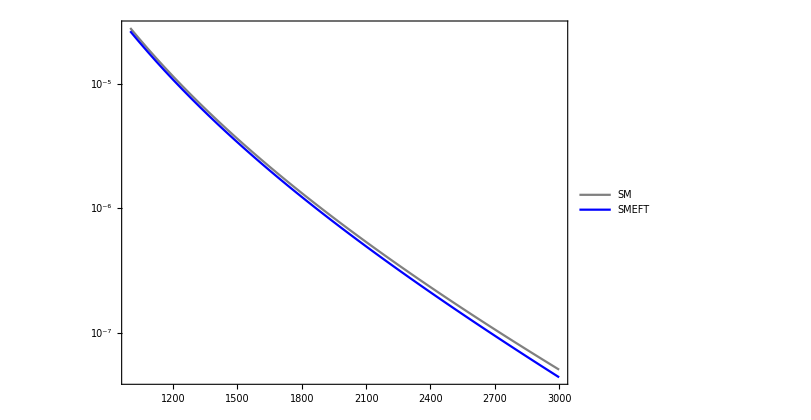

```mathematica
legend=Placed[LineLegend[{"SM","SMEFT"},LegendFunction->(Framed[#,Background->White]&),LegendMargins->5,LegendLayout->"Column"],{0.9,0.9}];
plot2=LogPlot[{dσdMdilepSMinterpol[M],dσdMdilepSMEFTinterpol[M]},{M,1000,3000},PlotStyle->{Gray,Blue},PlotLegends->legend]
Export["/Users/Tae/Desktop/GeoSMEFT/Amp_method_result/alpha_scheme_pp2ll_SMvsSMEFT.pdf",plot2];
```

## Checking (Junks + Compare w/ Adam’s + Old result)

```mathematica
monolepton=2π ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/alpha_scheme-udbar2lpv_X-sec.txt"]];
Integrate[SeriesCoefficient[monolepton,{x,0,0}],{Cθ,-1,1}]/.Ein->M/2//Simplify
```

(38308.2 M^2)/(M^4-12789.2 M^2+4.09171×10^7)

```mathematica
σhatudbarOx0
```

(38308.2 M^2)/(M^4-12789.2 M^2+4.09171×10^7)

```mathematica
Integrate[SeriesCoefficient[monolepton,{x,0,1}],{Cθ,-1,1}]/.Ein->M/2//Simplify//Expand//Chop
```

(3.50122×10^8 CHD6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(1.4197×10^9 CHD6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(54752.5 CHD6til M^6)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(9.79865×10^8 CHL36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(3.13359×10^12 CHL36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(76616.3 CHL36til M^6)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(9.79865×10^8 CHQ36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(3.13227×10^12 CHQ36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(76616.3 CHQ36til M^6)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(7.67512×10^8 CHWB6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(3.11216×10^9 CHWB6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(120025. CHWB6til M^6)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(1.47011×10^9 CLQ36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(3.13492×10^12 CLQ36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(11.9814 CLQ36til M^8)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(229849. CLQ36til M^6)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(1.68316×10^9 δGF6 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(4.42943×10^12 δGF6 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(154863. δGF6 M^6)/((M^4-12789.2 M^2+4.09171×10^7)^2)

```mathematica
σhatudbarOx1
```

-(3.50122×10^8 CHD6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(54752.5 CHD6til M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(2.24173×10^12 CHD6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(76616.3 CHL36til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(1.32441×10^9 CHL36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(76616.3 CHQ36til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(2.64881×10^9 CHQ36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(7.67512×10^8 CHWB6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(120025. CHWB6til M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(4.91417×10^12 CHWB6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(11.9814 CLQ36til M^4)/(M^4-12789.2 M^2+4.09171×10^7)-(76616.3 CLQ36til M^2)/(M^4-12789.2 M^2+4.09171×10^7)-(2.97424×10^8 δGF6 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(154863. δGF6 M^2)/(M^4-12789.2 M^2+4.09171×10^7)+(1.90714×10^12 δGF6 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)

```mathematica
-((3.50122*10^8 CHD6til M^4)/(M^4-12789.2 M^2+4.09171*10^7)^2)-(54752.5 CHD6til M^2)/(M^4-12789.2 M^2+4.09171*10^7)+(2.24173*10^12 CHD6til M^2)/(M^4-12789.2 M^2+4.09171*10^7)^2+(76616.3 CHL36til M^2)/(M^4-12789.2 M^2+4.09171*10^7)-(1.32441*10^9 CHL36til M^2)/(M^4-12789.2 M^2+4.09171*10^7)^2+(76616.3 CHQ36til M^2)/(M^4-12789.2 M^2+4.09171*10^7)-(2.64881*10^9 CHQ36til M^2)/(M^4-12789.2 M^2+4.09171*10^7)^2-(7.67512*10^8 CHWB6til M^4)/(M^4-12789.2 M^2+4.09171*10^7)^2-(120025. CHWB6til M^2)/(M^4-12789.2 M^2+4.09171*10^7)+(4.91417*10^12 CHWB6til M^2)/(M^4-12789.2 M^2+4.09171*10^7)^2+(11.9814 CLQ36til M^4)/(M^4-12789.2 M^2+4.09171*10^7)-(76616.3 CLQ36til M^2)/(M^4-12789.2 M^2+4.09171*10^7)-(2.97424*10^8 δGF6 M^4)/(M^4-12789.2 M^2+4.09171*10^7)^2-(154863. δGF6 M^2)/(M^4-12789.2 M^2+4.09171*10^7)+(1.90714*10^12 δGF6 M^2)/(M^4-12789.2 M^2+4.09171*10^7)^2-((3.50122*10^8 CHD6til M^4)/(M^4-12789.2 M^2+4.09171*10^7)^2+(1.4197*10^9 CHD6til M^2)/(M^4-12789.2 M^2+4.09171*10^7)^2-(54752.5 CHD6til M^6)/(M^4-12789.2 M^2+4.09171*10^7)^2-(9.79865*10^8 CHL36til M^4)/(M^4-12789.2 M^2+4.09171*10^7)^2+(3.13359*10^12 CHL36til M^2)/(M^4-12789.2 M^2+4.09171*10^7)^2+(76616.3 CHL36til M^6)/(M^4-12789.2 M^2+4.09171*10^7)^2-(9.79865*10^8 CHQ36til M^4)/(M^4-12789.2 M^2+4.09171*10^7)^2+(3.13227*10^12 CHQ36til M^2)/(M^4-12789.2 M^2+4.09171*10^7)^2+(76616.3 CHQ36til M^6)/(M^4-12789.2 M^2+4.09171*10^7)^2+(7.67512*10^8 CHWB6til M^4)/(M^4-12789.2 M^2+4.09171*10^7)^2+(3.11216*10^9 CHWB6til M^2)/(M^4-12789.2 M^2+4.09171*10^7)^2-(120025. CHWB6til M^6)/(M^4-12789.2 M^2+4.09171*10^7)^2+(1.47011*10^9 CLQ36til M^4)/(M^4-12789.2 M^2+4.09171*10^7)^2-(3.13492*10^12 CLQ36til M^2)/(M^4-12789.2 M^2+4.09171*10^7)^2+(11.9814 CLQ36til M^8)/(M^4-12789.2 M^2+4.09171*10^7)^2-(229849. CLQ36til M^6)/(M^4-12789.2 M^2+4.09171*10^7)^2+(1.68316*10^9 δGF6 M^4)/(M^4-12789.2 M^2+4.09171*10^7)^2-(4.42943*10^12 δGF6 M^2)/(M^4-12789.2 M^2+4.09171*10^7)^2-(154863. δGF6 M^6)/(M^4-12789.2 M^2+4.09171*10^7)^2)//Simplify//Expand
```

-(3327. CHD6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(3.21775×10^6 CHD6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(3816.04 CHL36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(2.39873×10^6 CHL36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(3816.04 CHQ36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(2.00127×10^6 CHQ36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(270. CHWB6til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(1.70875×10^7 CHWB6til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(4674.1 CLQ36til M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(3.19127×10^6 CLQ36til M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(0.17912 CLQ36til M^6)/((M^4-12789.2 M^2+4.09171×10^7)^2)-(10120.4 δGF6 M^4)/((M^4-12789.2 M^2+4.09171×10^7)^2)+(2.51427×10^7 δGF6 M^2)/((M^4-12789.2 M^2+4.09171×10^7)^2)